```mathematica
Exit[]
```

### MAPK scaffold pnas model from txt files

```mathematica
SetDirectory["/home/abergman/dicty/scaffold/"];
txt=Import["text equations","Text"];
txt=StringReplace[txt,{"d/dt"->"","[t] = "->"'[t] == ","*"->"p","-Ptot"->"Phtot","-P)"->"Ph)","-Ktot"->"Ktot","-K"->"Ki","â"->"-","-GTP"->"","kr1"->"k5","kr2"->"k9"}];
txt=StringReplace[txt,ShortestMatch["("~~a:LetterCharacter..~~" "~~b:LetterCharacter..~~")"]:>a<>b];
eq=ToExpression/@StringSplit[txt,","];
txt=Import["text params","Text"];
txt=StringReplace[txt,{"MAPKKK"->"RAF","MAPKK"->"MEK"," K-ase"->"Ktot"," P-ase"->"Phtot","["|"]"->"","off"->"of"}];
params=Import[StringToStream[txt],"Table"];
params=ToExpression[params];
params=Complement[params,{{}}];
params=Rule@@#&/@params;
params=params/.Rule[RAFKtot,r_]->Rule[RAFKtot,r*UnitStep[t]];
tstart=-1000;
ic=eq[[All,1]]/.Derivative[1]->Identity/.t->tstart;
ic=Thread[ic==0];
ic=ic/.{RAF[t_]==0->RAF[t]==RAFtot,MEK[t_]==0->MEK[t]==MEKtot,MAPK[t_]==0->MAPK[t]==MAPKtot,C1[t_]==0->C1[t]==C1tot};
```

### MAPK scaffold pnas model from expressions

```mathematica
eq={RAF'[t]==k2 RAFpRAFPh[t]-a1 RAF[t] (RAFKtot-RAFRAFKi[t])+d1 RAFRAFKi[t],RAFRAFKi'[t]==a1 RAF[t] (RAFKtot-RAFRAFKi[t])-(d1+k1) RAFRAFKi[t],RAFp'[t]==(d5+k5) MEKpRAFp[t]+(d3+k3) MEKRAFp[t]-a3 MEK[t] RAFp[t]-a5 MEKp[t] RAFp[t]-a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])+d2 RAFpRAFPh[t]+k1 RAFRAFKi[t],RAFpRAFPh'[t]==a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])-(d2+k2) RAFpRAFPh[t],MEK'[t]==of1 (C2[t]+C6[t]+C9[t])-on1 (C1[t]+C4[t]+C5[t]) MEK[t]+k4 MEKpMEKPh[t]+d3 MEKRAFp[t]-a3 MEK[t] RAFp[t],MEKRAFp'[t]==-(d3+k3) MEKRAFp[t]+a3 MEK[t] RAFp[t],MEKp'[t]==d4 MEKpMEKPh[t]-a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+k6 MEKppMEKPh[t]+d5 MEKpRAFp[t]+k3 MEKRAFp[t]-a5 MEKp[t] RAFp[t],MEKpMEKPh'[t]==-(d4+k4) MEKpMEKPh[t]+a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t]),MEKpRAFp'[t]==-(d5+k5) MEKpRAFp[t]+a5 MEKp[t] RAFp[t],MEKpp'[t]==of3 (C3[t]+C7[t]+C8[t])+(d7+k7) MAPKMEKpp[t]+(d9+k9) MAPKpMEKpp[t]-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+d6 MEKppMEKPh[t]+k5 MEKpRAFp[t],MEKppMEKPh'[t]==a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])-(d6+k6) MEKppMEKPh[t],MAPK'[t]==of2 (C4[t]+C6[t]+C7[t])-on2 (C1[t]+C2[t]+C3[t]) MAPK[t]+d7 MAPKMEKpp[t]+k8 MAPKpMAPKPh[t]-a7 MAPK[t] MEKpp[t],MAPKMEKpp'[t]==-(d7+k7) MAPKMEKpp[t]+a7 MAPK[t] MEKpp[t],MAPKp'[t]==k7 MAPKMEKpp[t]+d8 MAPKpMAPKPh[t]+d9 MAPKpMEKpp[t]-a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+k10 MAPKppMAPKPh[t]-a9 MAPKp[t] MEKpp[t],MAPKpMEKpp'[t]==-(d9+k9) MAPKpMEKpp[t]+a9 MAPKp[t] MEKpp[t],MAPKpp'[t]==of4 (C5[t]+C8[t]+C9[t])+k9 MAPKpMEKpp[t]-a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+d10 MAPKppMAPKPh[t],MAPKpMAPKPh'[t]==-(d8+k8) MAPKpMAPKPh[t]+a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t]),MAPKppMAPKPh'[t]==a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])-(d10+k10) MAPKppMAPKPh[t],C1'[t]==of1 C2[t]+of3 C3[t]+of2 C4[t]+of4 C5[t]-C1[t] (on2 MAPK[t]+on1 MEK[t]),C2'[t]==of2 C6[t]+of4 C9[t]-C2[t] (of1+on2 MAPK[t])+on1 C1[t] MEK[t]-k5 C2[t] RAFp[t],C3'[t]==-of3 C3[t]+of2 C7[t]+of4 C8[t]-on2 C3[t] MAPK[t]+k5 C2[t] RAFp[t],C4'[t]==of1 C6[t]+of3 C7[t]+on2 C1[t] MAPK[t]-C4[t] (of2+on1 MEK[t]),C5'[t]==of3 C8[t]+of1 C9[t]-C5[t] (of4+on1 MEK[t]),C6'[t]==-(of1+of2) C6[t]+on2 C2[t] MAPK[t]+on1 C4[t] MEK[t]-k5 C6[t] RAFp[t],C7'[t]==-k9 C7[t]-of2 C7[t]-of3 C7[t]+on2 C3[t] MAPK[t]+k5 C6[t] RAFp[t],C8'[t]==k9 C7[t]-(of3+of4) C8[t]+k5 C9[t] RAFp[t],C9'[t]==-(of1+of4) C9[t]+on1 C5[t] MEK[t]-k5 C9[t] RAFp[t]};
```

```mathematica
params={a1->1,a10->5,a2->0.5,a3->3.3,a4->10,a5->3.3,a6->10,a7->20,a8->5,a9->20,C1tot->0,d1->0.4,d10->0.4,d2->0.5,d3->0.42,d4->0.8,d5->0.4,d6->0.8,d7->0.6,d8->0.4,d9->0.6,k1->0.1,k10->0.1,k2->0.1,k3->0.1,k4->0.1,k5->0.1,k6->0.1,k7->0.1,k8->0.1,k9->0.1,MAPKPhtot->0.3,MAPKtot->0.4,MEKPhtot->0.2,MEKtot->0.2,of1->0.05,of2->0.05,of3->0.05,of4->0.5,on1->10,on2->10,RAFKtot->0.2 UnitStep[t],RAFPhtot->0.3,RAFtot->0.3};
```

```mathematica
tstart=-1000;
ic={RAF[-1000]==RAFtot,RAFRAFKi[-1000]==0,RAFp[-1000]==0,RAFpRAFPh[-1000]==0,MEK[-1000]==MEKtot,MEKRAFp[-1000]==0,MEKp[-1000]==0,MEKpMEKPh[-1000]==0,MEKpRAFp[-1000]==0,MEKpp[-1000]==0,MEKppMEKPh[-1000]==0,MAPK[-1000]==MAPKtot,MAPKMEKpp[-1000]==0,MAPKp[-1000]==0,MAPKpMEKpp[-1000]==0,MAPKpp[-1000]==0,MAPKpMAPKPh[-1000]==0,MAPKppMAPKPh[-1000]==0,C1[-1000]==C1tot,C2[-1000]==0,C3[-1000]==0,C4[-1000]==0,C5[-1000]==0,C6[-1000]==0,C7[-1000]==0,C8[-1000]==0,C9[-1000]==0};
```

### Scaffold cyto-mem-vesc

```mathematica
equ=Drop[eq,4];
```

```mathematica
FluxCM=p1*Scyto[t]-p2*Smem[t];
FluxMV=p3*Smem[t];
FluxVC=p4*C1[t];
```

```mathematica
equ=equ/.C1'[t]==q_:>C1'[t]==q+(FluxMV-FluxVC);
```

```mathematica
equ=Join[equ,
{Scyto'[t]==FluxVC-FluxCM,
Smem'[t]==FluxCM-FluxMV}];
```

```mathematica
TableForm[equ]
```

MEK'[t]==of1 (C2[t]+C6[t]+C9[t])-on1 (C1[t]+C4[t]+C5[t]) MEK[t]+k4 MEKpMEKPh[t]+d3 MEKRAFp[t]-a3 MEK[t] RAFp[t]
MEKRAFp'[t]==(-d3-k3) MEKRAFp[t]+a3 MEK[t] RAFp[t]
MEKp'[t]==d4 MEKpMEKPh[t]-a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+k6 MEKppMEKPh[t]+d5 MEKpRAFp[t]+k3 MEKRAFp[t]-a5 MEKp[t] RAFp[t]
MEKpMEKPh'[t]==(-d4-k4) MEKpMEKPh[t]+a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])
MEKpRAFp'[t]==(-d5-k5) MEKpRAFp[t]+a5 MEKp[t] RAFp[t]
MEKpp'[t]==of3 (C3[t]+C7[t]+C8[t])+(d7+k7) MAPKMEKpp[t]+(d9+k9) MAPKpMEKpp[t]-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+d6 MEKppMEKPh[t]+k5 MEKpRAFp[t]
MEKppMEKPh'[t]==a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])-(d6+k6) MEKppMEKPh[t]
MAPK'[t]==of2 (C4[t]+C6[t]+C7[t])-on2 (C1[t]+C2[t]+C3[t]) MAPK[t]+d7 MAPKMEKpp[t]+k8 MAPKpMAPKPh[t]-a7 MAPK[t] MEKpp[t]
MAPKMEKpp'[t]==(-d7-k7) MAPKMEKpp[t]+a7 MAPK[t] MEKpp[t]
MAPKp'[t]==k7 MAPKMEKpp[t]+d8 MAPKpMAPKPh[t]+d9 MAPKpMEKpp[t]-a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+k10 MAPKppMAPKPh[t]-a9 MAPKp[t] MEKpp[t]
MAPKpMEKpp'[t]==(-d9-k9) MAPKpMEKpp[t]+a9 MAPKp[t] MEKpp[t]
MAPKpp'[t]==of4 (C5[t]+C8[t]+C9[t])+k9 MAPKpMEKpp[t]-a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+d10 MAPKppMAPKPh[t]
MAPKpMAPKPh'[t]==(-d8-k8) MAPKpMAPKPh[t]+a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])
MAPKppMAPKPh'[t]==a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])-(d10+k10) MAPKppMAPKPh[t]
C1'[t]==-p4 C1[t]+of1 C2[t]+of3 C3[t]+of2 C4[t]+of4 C5[t]-C1[t] (on2 MAPK[t]+on1 MEK[t])+p3 Smem[t]
C2'[t]==of2 C6[t]+of4 C9[t]-C2[t] (of1+on2 MAPK[t])+on1 C1[t] MEK[t]-k5 C2[t] RAFp[t]
C3'[t]==-of3 C3[t]+of2 C7[t]+of4 C8[t]-on2 C3[t] MAPK[t]+k5 C2[t] RAFp[t]
C4'[t]==of1 C6[t]+of3 C7[t]+on2 C1[t] MAPK[t]-C4[t] (of2+on1 MEK[t])
C5'[t]==of3 C8[t]+of1 C9[t]-C5[t] (of4+on1 MEK[t])
C6'[t]==(-of1-of2) C6[t]+on2 C2[t] MAPK[t]+on1 C4[t] MEK[t]-k5 C6[t] RAFp[t]
C7'[t]==-k9 C7[t]-of2 C7[t]-of3 C7[t]+on2 C3[t] MAPK[t]+k5 C6[t] RAFp[t]
C8'[t]==k9 C7[t]-(of3+of4) C8[t]+k5 C9[t] RAFp[t]
C9'[t]==(-of1-of4) C9[t]+on1 C5[t] MEK[t]-k5 C9[t] RAFp[t]
Scyto'[t]==p4 C1[t]-p1 Scyto[t]+p2 Smem[t]
Smem'[t]==p1 Scyto[t]-p2 Smem[t]-p3 Smem[t]

```mathematica
params=params/.Rule[RAFKtot,_]->Rule[RAFp,0.14];
params=Join[params,{p1->1,p2->1,p3->1,p4->1}];
```

```mathematica
equ[[All,2]]/.{x_'[t]->0,x_[t]->x}/.(params/.Rule[x_,_]->Rule[x,1])/.(equ[[All,1]]/.x_'[t]->Rule[x,1])
```

{1,-1,4,-3,-1,8,-3,1,-1,4,-1,6,-3,-3,2,0,1,1,0,-1,-1,0,-2,1,-1}

### SS

```mathematica
vars=equ[[All,1]];
vars=vars/.x_'[t]->x;
MEKtotequ=StringCases[ToString/@vars,___~~"MEK"~~___]//ToExpression//Flatten//Total;
MEKtotequ+=C2+C3+C6+C7+C8+C9;
MAPKtotequ=StringCases[ToString/@vars,___~~"MAPK"~~___]//ToExpression//Flatten//Total;
MAPKtotequ+=C4+C5+C6+C7+C8+C9;

equ=DeleteCases[equ,MEK'[t]==_];
equ=Append[equ,MEKtot==MEKtotequ];
equ=DeleteCases[equ,MAPK'[t]==_];
equ=Append[equ,MAPKtot==MAPKtotequ];
equ=DeleteCases[equ,C1'[t]==_];
equ=Append[equ,Stot==C1+C2+C3+C4+C5+C6+C7+C8+Scyto+Smem];
params=params/.C1tot->Stot;
equ=equ/.{x_'[t]->0,x_[t]->x};

TableForm[equ]
```

0==(-d3-k3) MEKRAFp+a3 MEK RAFp
0==d4 MEKpMEKPh-a4 MEKp (MEKPhtot-MEKpMEKPh-MEKppMEKPh)+k6 MEKppMEKPh+d5 MEKpRAFp+k3 MEKRAFp-a5 MEKp RAFp
0==(-d4-k4) MEKpMEKPh+a4 MEKp (MEKPhtot-MEKpMEKPh-MEKppMEKPh)
0==(-d5-k5) MEKpRAFp+a5 MEKp RAFp
0==(d7+k7) MAPKMEKpp+(d9+k9) MAPKpMEKpp-a7 MAPK MEKpp-a9 MAPKp MEKpp-a6 MEKpp (MEKPhtot-MEKpMEKPh-MEKppMEKPh)+d6 MEKppMEKPh+k5 MEKpRAFp+(C3+C7+C8) of3
0==a6 MEKpp (MEKPhtot-MEKpMEKPh-MEKppMEKPh)-(d6+k6) MEKppMEKPh
0==(-d7-k7) MAPKMEKpp+a7 MAPK MEKpp
0==k7 MAPKMEKpp+d8 MAPKpMAPKPh+d9 MAPKpMEKpp-a8 MAPKp (MAPKPhtot-MAPKpMAPKPh-MAPKppMAPKPh)+k10 MAPKppMAPKPh-a9 MAPKp MEKpp
0==(-d9-k9) MAPKpMEKpp+a9 MAPKp MEKpp
0==k9 MAPKpMEKpp-a10 MAPKpp (MAPKPhtot-MAPKpMAPKPh-MAPKppMAPKPh)+d10 MAPKppMAPKPh+(C5+C8+C9) of4
0==(-d8-k8) MAPKpMAPKPh+a8 MAPKp (MAPKPhtot-MAPKpMAPKPh-MAPKppMAPKPh)
0==a10 MAPKpp (MAPKPhtot-MAPKpMAPKPh-MAPKppMAPKPh)-(d10+k10) MAPKppMAPKPh
0==C6 of2+C9 of4+C1 MEK on1-C2 (of1+MAPK on2)-C2 k5 RAFp
0==C7 of2-C3 of3+C8 of4-C3 MAPK on2+C2 k5 RAFp
0==C6 of1+C7 of3-C4 (of2+MEK on1)+C1 MAPK on2
0==C9 of1+C8 of3-C5 (of4+MEK on1)
0==C6 (-of1-of2)+C4 MEK on1+C2 MAPK on2-C6 k5 RAFp
0==-C7 k9-C7 of2-C7 of3+C3 MAPK on2+C6 k5 RAFp
0==C7 k9-C8 (of3+of4)+C9 k5 RAFp
0==C9 (-of1-of4)+C5 MEK on1-C9 k5 RAFp
0==C1 p4-p1 Scyto+p2 Smem
0==p1 Scyto-p2 Smem-p3 Smem
MEKtot==C2+C3+C6+C7+C8+C9+MAPKMEKpp+MAPKpMEKpp+MEK+MEKp+MEKpMEKPh+MEKpp+MEKppMEKPh+MEKpRAFp+MEKRAFp
MAPKtot==C4+C5+C6+C7+C8+C9+MAPK+MAPKMEKpp+MAPKp+MAPKpMAPKPh+MAPKpMEKpp+MAPKpp+MAPKppMAPKPh
Stot==C1+C2+C3+C4+C5+C6+C7+C8+Scyto+Smem

### runsim

```mathematica
FindRoot[equ/.params,Thread[{vars,0}]]
```

{MEK→0.0306145,MEKRAFp→0.0271998,MEKp→0.0154416,MEKpMEKPh→0.0271998,MEKpRAFp→0.014268,MEKpp→0.00810006,MEKppMEKPh→0.014268,MAPK→0.24765,MAPKMEKpp→0.0573137,MAPKp→0.0241737,MAPKpMEKpp→0.00559451,MAPKpp→0.00235964,MAPKpMAPKPh→0.0573137,MAPKppMAPKPh→0.00559451,C1→0.,C2→0.,C3→0.,C4→0.,C5→0.,C6→0.,C7→0.,C8→0.,C9→0.,Scyto→0.,Smem→0.}

```mathematica
runsim$init=Thread[{vars,0}];
runsim[p___]:=Module[{sol},
sol=FindRoot[equ/.Flatten[{p}]/.params,runsim$init,MaxIterations->∞];
runsim$init=Thread[{vars,vars/.sol}];
sol
]
runsim[]
```

{MEK→0.0306145,MEKRAFp→0.0271998,MEKp→0.0154416,MEKpMEKPh→0.0271998,MEKpRAFp→0.014268,MEKpp→0.00810006,MEKppMEKPh→0.014268,MAPK→0.24765,MAPKMEKpp→0.0573137,MAPKp→0.0241737,MAPKpMEKpp→0.00559451,MAPKpp→0.00235964,MAPKpMAPKPh→0.0573137,MAPKppMAPKPh→0.00559451,C1→0.,C2→0.,C3→0.,C4→0.,C5→0.,C6→0.,C7→0.,C8→0.,C9→0.,Scyto→0.,Smem→0.}

{{0.,0.00235964},{0.05,0.00553232},{0.1,0.0077924},{0.15,0.00885179},{0.2,0.00909676},{0.25,0.00887219},{0.3,0.00831976},{0.35,0.00754847},{0.4,0.00671516},{0.45,0.00594881},{0.5,0.00529644},{0.55,0.00475487},{0.6,0.00430588},{0.65,0.00393076},{0.7,0.00361402},{0.75,0.00334365},{0.8,0.00311047},{0.85,0.00290745},{0.9,0.00272917},{0.95,0.00257143},{1.,0.00243088},{1.05,0.00230489},{1.1,0.0021913},{1.15,0.00208838},{1.2,0.00199469},{1.25,0.00190905},{1.3,0.00183046},{1.35,0.00175809},{1.4,0.00169123},{1.45,0.00162927},{1.5,0.00157169},{1.55,0.00151805},{1.6,0.00146795},{1.65,0.00142105},{1.7,0.00137706},{1.75,0.00133571},{1.8,0.00129678},{1.85,0.00126005},{1.9,0.00122534},{1.95,0.0011925},{2.,0.00116137}}

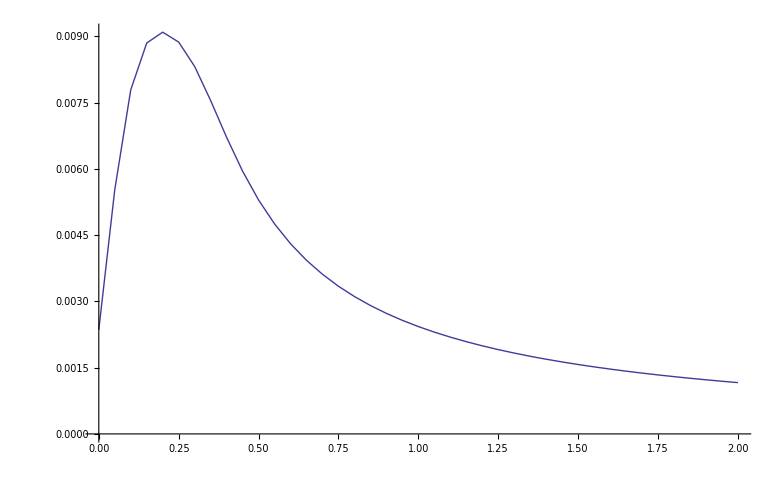

```mathematica
dat={#,MAPKpp}/.runsim[Stot->#,p2->0,p4->0]&/@Range[0,2,0.05]
ListLinePlot[dat]
```

### Front-back compartments

```mathematica
len=2;
params=params/.Rule[RAFKtot,_]->Rule[RAFp,0.14]/.C1tot->Stot;
params=Join[params,{p2->1,p4->1,Di->0.001}];
params=Flatten[{params,Array[{p1[#]->1,p3[#]->1}&,len,0]}];
```

```mathematica
params
```

{a1→1,a10→5,a2→0.5,a3→3.3,a4→10,a5→3.3,a6→10,a7→20,a8→5,a9→20,Stot→0,d1→0.4,d10→0.4,d2→0.5,d3→0.42,d4→0.8,d5→0.4,d6→0.8,d7→0.6,d8→0.4,d9→0.6,k1→0.1,k10→0.1,k2→0.1,k3→0.1,k4→0.1,k5→0.1,k6→0.1,k7→0.1,k8→0.1,k9→0.1,MAPKPhtot→0.3,MAPKtot→0.4,MEKPhtot→0.2,MEKtot→0.2,of1→0.05,of2→0.05,of3→0.05,of4→0.5,on1→10,on2→10,RAFp→0.14,RAFPhtot→0.3,RAFtot→0.3,p2→1,p4→1,Di→0.001,p1[0]→1,p3[0]→1,p1[1]→1,p3[1]→1}

```mathematica
equ=Drop[eq,4];
equ=equ/.RAFp[t]->RAFp;
FluxCM=p1[s]*Scyto[t]-p2*Smem[t];
FluxMV=p3[s]*Smem[t];
FluxVC=p4*C1[t];
equ=equ/.C1'[t]==q_:>C1'[t]==q+(FluxMV-FluxVC);
equ=Join[
{Scyto'[t]==FluxVC-FluxCM},
equ,
{Smem'[t]==FluxCM-FluxMV}];
vars=equ[[All,1]];
vars=vars/.x_'[t]->x;
equ=equ/.Thread[vars->(#[s]&/@vars)];
equ=equ/.v_[s]'[t]==lhs_/;FreeQ[v,C1|C2|C3|C4|C5|C6|C7|C8|C9|Smem]->v[s]'[t]==lhs+Di(v[s-1][t]-2v[s][t]+v[s+1][t]);

equ=Flatten@Table[equ,{s,0,len-1}];
equ=equ/.{x_[-1][t]->x[0][t],x_[len][t]->x[len-1][t]};
vars=equ/.v_'[t]==_->v;
TableForm[equ]
equODE=equ;
varODE=vars;
```

Scyto[0]'[t]==p4 C1[0][t]-p1[0] Scyto[0][t]+Di (-Scyto[0][t]+Scyto[1][t])+p2 Smem[0][t]
MEK[0]'[t]==of1 (C2[0][t]+C6[0][t]+C9[0][t])-a3 RAFp MEK[0][t]-on1 (C1[0][t]+C4[0][t]+C5[0][t]) MEK[0][t]+Di (-MEK[0][t]+MEK[1][t])+k4 MEKpMEKPh[0][t]+d3 MEKRAFp[0][t]
MEKRAFp[0]'[t]==a3 RAFp MEK[0][t]+(-d3-k3) MEKRAFp[0][t]+Di (-MEKRAFp[0][t]+MEKRAFp[1][t])
MEKp[0]'[t]==-a5 RAFp MEKp[0][t]+Di (-MEKp[0][t]+MEKp[1][t])+d4 MEKpMEKPh[0][t]-a4 MEKp[0][t] (MEKPhtot-MEKpMEKPh[0][t]-MEKppMEKPh[0][t])+k6 MEKppMEKPh[0][t]+d5 MEKpRAFp[0][t]+k3 MEKRAFp[0][t]
MEKpMEKPh[0]'[t]==(-d4-k4) MEKpMEKPh[0][t]+Di (-MEKpMEKPh[0][t]+MEKpMEKPh[1][t])+a4 MEKp[0][t] (MEKPhtot-MEKpMEKPh[0][t]-MEKppMEKPh[0][t])
MEKpRAFp[0]'[t]==a5 RAFp MEKp[0][t]+(-d5-k5) MEKpRAFp[0][t]+Di (-MEKpRAFp[0][t]+MEKpRAFp[1][t])
MEKpp[0]'[t]==of3 (C3[0][t]+C7[0][t]+C8[0][t])+(d7+k7) MAPKMEKpp[0][t]+(d9+k9) MAPKpMEKpp[0][t]-a7 MAPK[0][t] MEKpp[0][t]-a9 MAPKp[0][t] MEKpp[0][t]+Di (-MEKpp[0][t]+MEKpp[1][t])-a6 MEKpp[0][t] (MEKPhtot-MEKpMEKPh[0][t]-MEKppMEKPh[0][t])+d6 MEKppMEKPh[0][t]+k5 MEKpRAFp[0][t]
MEKppMEKPh[0]'[t]==a6 MEKpp[0][t] (MEKPhtot-MEKpMEKPh[0][t]-MEKppMEKPh[0][t])-(d6+k6) MEKppMEKPh[0][t]+Di (-MEKppMEKPh[0][t]+MEKppMEKPh[1][t])
MAPK[0]'[t]==of2 (C4[0][t]+C6[0][t]+C7[0][t])-on2 (C1[0][t]+C2[0][t]+C3[0][t]) MAPK[0][t]+Di (-MAPK[0][t]+MAPK[1][t])+d7 MAPKMEKpp[0][t]+k8 MAPKpMAPKPh[0][t]-a7 MAPK[0][t] MEKpp[0][t]
MAPKMEKpp[0]'[t]==(-d7-k7) MAPKMEKpp[0][t]+Di (-MAPKMEKpp[0][t]+MAPKMEKpp[1][t])+a7 MAPK[0][t] MEKpp[0][t]
MAPKp[0]'[t]==k7 MAPKMEKpp[0][t]+Di (-MAPKp[0][t]+MAPKp[1][t])+d8 MAPKpMAPKPh[0][t]+d9 MAPKpMEKpp[0][t]-a8 MAPKp[0][t] (MAPKPhtot-MAPKpMAPKPh[0][t]-MAPKppMAPKPh[0][t])+k10 MAPKppMAPKPh[0][t]-a9 MAPKp[0][t] MEKpp[0][t]
MAPKpMEKpp[0]'[t]==(-d9-k9) MAPKpMEKpp[0][t]+Di (-MAPKpMEKpp[0][t]+MAPKpMEKpp[1][t])+a9 MAPKp[0][t] MEKpp[0][t]
MAPKpp[0]'[t]==of4 (C5[0][t]+C8[0][t]+C9[0][t])+k9 MAPKpMEKpp[0][t]+Di (-MAPKpp[0][t]+MAPKpp[1][t])-a10 MAPKpp[0][t] (MAPKPhtot-MAPKpMAPKPh[0][t]-MAPKppMAPKPh[0][t])+d10 MAPKppMAPKPh[0][t]
MAPKpMAPKPh[0]'[t]==(-d8-k8) MAPKpMAPKPh[0][t]+Di (-MAPKpMAPKPh[0][t]+MAPKpMAPKPh[1][t])+a8 MAPKp[0][t] (MAPKPhtot-MAPKpMAPKPh[0][t]-MAPKppMAPKPh[0][t])
MAPKppMAPKPh[0]'[t]==a10 MAPKpp[0][t] (MAPKPhtot-MAPKpMAPKPh[0][t]-MAPKppMAPKPh[0][t])-(d10+k10) MAPKppMAPKPh[0][t]+Di (-MAPKppMAPKPh[0][t]+MAPKppMAPKPh[1][t])
C1[0]'[t]==-p4 C1[0][t]+of1 C2[0][t]+of3 C3[0][t]+of2 C4[0][t]+of4 C5[0][t]-C1[0][t] (on2 MAPK[0][t]+on1 MEK[0][t])+p3[0] Smem[0][t]
C2[0]'[t]==-k5 RAFp C2[0][t]+of2 C6[0][t]+of4 C9[0][t]-C2[0][t] (of1+on2 MAPK[0][t])+on1 C1[0][t] MEK[0][t]
C3[0]'[t]==k5 RAFp C2[0][t]-of3 C3[0][t]+of2 C7[0][t]+of4 C8[0][t]-on2 C3[0][t] MAPK[0][t]
C4[0]'[t]==of1 C6[0][t]+of3 C7[0][t]+on2 C1[0][t] MAPK[0][t]-C4[0][t] (of2+on1 MEK[0][t])
C5[0]'[t]==of3 C8[0][t]+of1 C9[0][t]-C5[0][t] (of4+on1 MEK[0][t])
C6[0]'[t]==(-of1-of2) C6[0][t]-k5 RAFp C6[0][t]+on2 C2[0][t] MAPK[0][t]+on1 C4[0][t] MEK[0][t]
C7[0]'[t]==k5 RAFp C6[0][t]-k9 C7[0][t]-of2 C7[0][t]-of3 C7[0][t]+on2 C3[0][t] MAPK[0][t]
C8[0]'[t]==k9 C7[0][t]-(of3+of4) C8[0][t]+k5 RAFp C9[0][t]
C9[0]'[t]==(-of1-of4) C9[0][t]-k5 RAFp C9[0][t]+on1 C5[0][t] MEK[0][t]
Smem[0]'[t]==p1[0] Scyto[0][t]-p2 Smem[0][t]-p3[0] Smem[0][t]
Scyto[1]'[t]==p4 C1[1][t]+Di (Scyto[0][t]-Scyto[1][t])-p1[1] Scyto[1][t]+p2 Smem[1][t]
MEK[1]'[t]==of1 (C2[1][t]+C6[1][t]+C9[1][t])+Di (MEK[0][t]-MEK[1][t])-a3 RAFp MEK[1][t]-on1 (C1[1][t]+C4[1][t]+C5[1][t]) MEK[1][t]+k4 MEKpMEKPh[1][t]+d3 MEKRAFp[1][t]
MEKRAFp[1]'[t]==a3 RAFp MEK[1][t]+Di (MEKRAFp[0][t]-MEKRAFp[1][t])+(-d3-k3) MEKRAFp[1][t]
MEKp[1]'[t]==Di (MEKp[0][t]-MEKp[1][t])-a5 RAFp MEKp[1][t]+d4 MEKpMEKPh[1][t]-a4 MEKp[1][t] (MEKPhtot-MEKpMEKPh[1][t]-MEKppMEKPh[1][t])+k6 MEKppMEKPh[1][t]+d5 MEKpRAFp[1][t]+k3 MEKRAFp[1][t]
MEKpMEKPh[1]'[t]==Di (MEKpMEKPh[0][t]-MEKpMEKPh[1][t])+(-d4-k4) MEKpMEKPh[1][t]+a4 MEKp[1][t] (MEKPhtot-MEKpMEKPh[1][t]-MEKppMEKPh[1][t])
MEKpRAFp[1]'[t]==a5 RAFp MEKp[1][t]+Di (MEKpRAFp[0][t]-MEKpRAFp[1][t])+(-d5-k5) MEKpRAFp[1][t]
MEKpp[1]'[t]==of3 (C3[1][t]+C7[1][t]+C8[1][t])+(d7+k7) MAPKMEKpp[1][t]+(d9+k9) MAPKpMEKpp[1][t]+Di (MEKpp[0][t]-MEKpp[1][t])-a7 MAPK[1][t] MEKpp[1][t]-a9 MAPKp[1][t] MEKpp[1][t]-a6 MEKpp[1][t] (MEKPhtot-MEKpMEKPh[1][t]-MEKppMEKPh[1][t])+d6 MEKppMEKPh[1][t]+k5 MEKpRAFp[1][t]
MEKppMEKPh[1]'[t]==a6 MEKpp[1][t] (MEKPhtot-MEKpMEKPh[1][t]-MEKppMEKPh[1][t])+Di (MEKppMEKPh[0][t]-MEKppMEKPh[1][t])-(d6+k6) MEKppMEKPh[1][t]
MAPK[1]'[t]==of2 (C4[1][t]+C6[1][t]+C7[1][t])+Di (MAPK[0][t]-MAPK[1][t])-on2 (C1[1][t]+C2[1][t]+C3[1][t]) MAPK[1][t]+d7 MAPKMEKpp[1][t]+k8 MAPKpMAPKPh[1][t]-a7 MAPK[1][t] MEKpp[1][t]
MAPKMEKpp[1]'[t]==Di (MAPKMEKpp[0][t]-MAPKMEKpp[1][t])+(-d7-k7) MAPKMEKpp[1][t]+a7 MAPK[1][t] MEKpp[1][t]
MAPKp[1]'[t]==k7 MAPKMEKpp[1][t]+Di (MAPKp[0][t]-MAPKp[1][t])+d8 MAPKpMAPKPh[1][t]+d9 MAPKpMEKpp[1][t]-a8 MAPKp[1][t] (MAPKPhtot-MAPKpMAPKPh[1][t]-MAPKppMAPKPh[1][t])+k10 MAPKppMAPKPh[1][t]-a9 MAPKp[1][t] MEKpp[1][t]
MAPKpMEKpp[1]'[t]==Di (MAPKpMEKpp[0][t]-MAPKpMEKpp[1][t])+(-d9-k9) MAPKpMEKpp[1][t]+a9 MAPKp[1][t] MEKpp[1][t]
MAPKpp[1]'[t]==of4 (C5[1][t]+C8[1][t]+C9[1][t])+k9 MAPKpMEKpp[1][t]+Di (MAPKpp[0][t]-MAPKpp[1][t])-a10 MAPKpp[1][t] (MAPKPhtot-MAPKpMAPKPh[1][t]-MAPKppMAPKPh[1][t])+d10 MAPKppMAPKPh[1][t]
MAPKpMAPKPh[1]'[t]==Di (MAPKpMAPKPh[0][t]-MAPKpMAPKPh[1][t])+(-d8-k8) MAPKpMAPKPh[1][t]+a8 MAPKp[1][t] (MAPKPhtot-MAPKpMAPKPh[1][t]-MAPKppMAPKPh[1][t])
MAPKppMAPKPh[1]'[t]==a10 MAPKpp[1][t] (MAPKPhtot-MAPKpMAPKPh[1][t]-MAPKppMAPKPh[1][t])+Di (MAPKppMAPKPh[0][t]-MAPKppMAPKPh[1][t])-(d10+k10) MAPKppMAPKPh[1][t]
C1[1]'[t]==-p4 C1[1][t]+of1 C2[1][t]+of3 C3[1][t]+of2 C4[1][t]+of4 C5[1][t]-C1[1][t] (on2 MAPK[1][t]+on1 MEK[1][t])+p3[1] Smem[1][t]
C2[1]'[t]==-k5 RAFp C2[1][t]+of2 C6[1][t]+of4 C9[1][t]-C2[1][t] (of1+on2 MAPK[1][t])+on1 C1[1][t] MEK[1][t]
C3[1]'[t]==k5 RAFp C2[1][t]-of3 C3[1][t]+of2 C7[1][t]+of4 C8[1][t]-on2 C3[1][t] MAPK[1][t]
C4[1]'[t]==of1 C6[1][t]+of3 C7[1][t]+on2 C1[1][t] MAPK[1][t]-C4[1][t] (of2+on1 MEK[1][t])
C5[1]'[t]==of3 C8[1][t]+of1 C9[1][t]-C5[1][t] (of4+on1 MEK[1][t])
C6[1]'[t]==(-of1-of2) C6[1][t]-k5 RAFp C6[1][t]+on2 C2[1][t] MAPK[1][t]+on1 C4[1][t] MEK[1][t]
C7[1]'[t]==k5 RAFp C6[1][t]-k9 C7[1][t]-of2 C7[1][t]-of3 C7[1][t]+on2 C3[1][t] MAPK[1][t]
C8[1]'[t]==k9 C7[1][t]-(of3+of4) C8[1][t]+k5 RAFp C9[1][t]
C9[1]'[t]==(-of1-of4) C9[1][t]-k5 RAFp C9[1][t]+on1 C5[1][t] MEK[1][t]
Smem[1]'[t]==p1[1] Scyto[1][t]-p2 Smem[1][t]-p3[1] Smem[1][t]

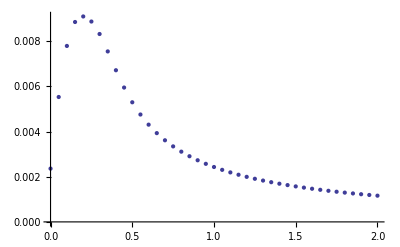

```mathematica
tend=1000;
dat=Function[C1tot,
ic=vars/.{MEK[s_]->MEK[s][0]==MEKtot,MAPK[s_]->MAPK[s][0]==MAPKtot,C1[s_]->C1[s][0]==C1tot,v_[s_]->v[s][0]==0};sol=NDSolve[Join[equ,ic]/.{p2->0,p4->0}/.params,vars,{t,0,tend}][[1]];
{C1tot,MAPKpp[1][tend]}/.sol
]/@Range[0,2,0.05];
ListPlot[dat]
```

```mathematica
MEKtotequ=StringCases[ToString/@vars,___~~"MEK"~~___]//ToExpression//Flatten//Total;
MEKtotequ+=Sum[C2[s]+C3[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
MAPKtotequ=StringCases[ToString/@vars,___~~"MAPK"~~___]//ToExpression//Flatten//Total;
MAPKtotequ+=Sum[C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
Stotequ=Sum[C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}];
equsubs=Flatten@{
Solve[len*MEKtot==MEKtotequ,MEK[0]],
Solve[len*MAPKtot==MAPKtotequ,MAPK[0]],
Solve[len*Stot==Stotequ,Scyto[0]]
};
TableForm[equsubs]
```

MEK[0]→2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1]
MAPK[0]→2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1]
Scyto[0]→2 Stot-C1[0]-C1[1]-C2[0]-C2[1]-C3[0]-C3[1]-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-Scyto[1]-Smem[0]-Smem[1]

```mathematica
equ=equODE/.{x_'[t]->0,x_[t]->x}/.equsubs;
TableForm[equ]
```

0==p4 C1[0]+p2 Smem[0]-p1[0] (2 Stot-C1[0]-C1[1]-C2[0]-C2[1]-C3[0]-C3[1]-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-Scyto[1]-Smem[0]-Smem[1])+Di (-2 Stot+C1[0]+C1[1]+C2[0]+C2[1]+C3[0]+C3[1]+C4[0]+C4[1]+C5[0]+C5[1]+C6[0]+C6[1]+C7[0]+C7[1]+C8[0]+C8[1]+C9[0]+C9[1]+2 Scyto[1]+Smem[0]+Smem[1])
0==of1 (C2[0]+C6[0]+C9[0])+k4 MEKpMEKPh[0]+d3 MEKRAFp[0]-a3 RAFp (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])-on1 (C1[0]+C4[0]+C5[0]) (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])+Di (-2 MEKtot+C2[0]+C2[1]+C3[0]+C3[1]+C6[0]+C6[1]+C7[0]+C7[1]+C8[0]+C8[1]+C9[0]+C9[1]+MAPKMEKpp[0]+MAPKMEKpp[1]+MAPKpMEKpp[0]+MAPKpMEKpp[1]+2 MEK[1]+MEKp[0]+MEKp[1]+MEKpMEKPh[0]+MEKpMEKPh[1]+MEKpp[0]+MEKpp[1]+MEKppMEKPh[0]+MEKppMEKPh[1]+MEKpRAFp[0]+MEKpRAFp[1]+MEKRAFp[0]+MEKRAFp[1])
0==(-d3-k3) MEKRAFp[0]+a3 RAFp (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])+Di (-MEKRAFp[0]+MEKRAFp[1])
0==-a5 RAFp MEKp[0]+Di (-MEKp[0]+MEKp[1])+d4 MEKpMEKPh[0]-a4 MEKp[0] (MEKPhtot-MEKpMEKPh[0]-MEKppMEKPh[0])+k6 MEKppMEKPh[0]+d5 MEKpRAFp[0]+k3 MEKRAFp[0]
0==(-d4-k4) MEKpMEKPh[0]+Di (-MEKpMEKPh[0]+MEKpMEKPh[1])+a4 MEKp[0] (MEKPhtot-MEKpMEKPh[0]-MEKppMEKPh[0])
0==a5 RAFp MEKp[0]+(-d5-k5) MEKpRAFp[0]+Di (-MEKpRAFp[0]+MEKpRAFp[1])
0==of3 (C3[0]+C7[0]+C8[0])+(d7+k7) MAPKMEKpp[0]+(d9+k9) MAPKpMEKpp[0]-a9 MAPKp[0] MEKpp[0]-a7 (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1]) MEKpp[0]+Di (-MEKpp[0]+MEKpp[1])-a6 MEKpp[0] (MEKPhtot-MEKpMEKPh[0]-MEKppMEKPh[0])+d6 MEKppMEKPh[0]+k5 MEKpRAFp[0]
0==a6 MEKpp[0] (MEKPhtot-MEKpMEKPh[0]-MEKppMEKPh[0])-(d6+k6) MEKppMEKPh[0]+Di (-MEKppMEKPh[0]+MEKppMEKPh[1])
0==of2 (C4[0]+C6[0]+C7[0])+d7 MAPKMEKpp[0]+k8 MAPKpMAPKPh[0]-on2 (C1[0]+C2[0]+C3[0]) (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])+Di (-2 MAPKtot+C4[0]+C4[1]+C5[0]+C5[1]+C6[0]+C6[1]+C7[0]+C7[1]+C8[0]+C8[1]+C9[0]+C9[1]+2 MAPK[1]+MAPKMEKpp[0]+MAPKMEKpp[1]+MAPKp[0]+MAPKp[1]+MAPKpMAPKPh[0]+MAPKpMAPKPh[1]+MAPKpMEKpp[0]+MAPKpMEKpp[1]+MAPKpp[0]+MAPKpp[1]+MAPKppMAPKPh[0]+MAPKppMAPKPh[1])-a7 (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1]) MEKpp[0]
0==(-d7-k7) MAPKMEKpp[0]+Di (-MAPKMEKpp[0]+MAPKMEKpp[1])+a7 (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1]) MEKpp[0]
0==k7 MAPKMEKpp[0]+Di (-MAPKp[0]+MAPKp[1])+d8 MAPKpMAPKPh[0]+d9 MAPKpMEKpp[0]-a8 MAPKp[0] (MAPKPhtot-MAPKpMAPKPh[0]-MAPKppMAPKPh[0])+k10 MAPKppMAPKPh[0]-a9 MAPKp[0] MEKpp[0]
0==(-d9-k9) MAPKpMEKpp[0]+Di (-MAPKpMEKpp[0]+MAPKpMEKpp[1])+a9 MAPKp[0] MEKpp[0]
0==of4 (C5[0]+C8[0]+C9[0])+k9 MAPKpMEKpp[0]+Di (-MAPKpp[0]+MAPKpp[1])-a10 MAPKpp[0] (MAPKPhtot-MAPKpMAPKPh[0]-MAPKppMAPKPh[0])+d10 MAPKppMAPKPh[0]
0==(-d8-k8) MAPKpMAPKPh[0]+Di (-MAPKpMAPKPh[0]+MAPKpMAPKPh[1])+a8 MAPKp[0] (MAPKPhtot-MAPKpMAPKPh[0]-MAPKppMAPKPh[0])
0==a10 MAPKpp[0] (MAPKPhtot-MAPKpMAPKPh[0]-MAPKppMAPKPh[0])-(d10+k10) MAPKppMAPKPh[0]+Di (-MAPKppMAPKPh[0]+MAPKppMAPKPh[1])
0==-p4 C1[0]+of1 C2[0]+of3 C3[0]+of2 C4[0]+of4 C5[0]-C1[0] (on2 (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])+on1 (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1]))+p3[0] Smem[0]
0==-k5 RAFp C2[0]+of2 C6[0]+of4 C9[0]-C2[0] (of1+on2 (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1]))+on1 C1[0] (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])
0==k5 RAFp C2[0]-of3 C3[0]+of2 C7[0]+of4 C8[0]-on2 C3[0] (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])
0==of1 C6[0]+of3 C7[0]+on2 C1[0] (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])-C4[0] (of2+on1 (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1]))
0==of3 C8[0]+of1 C9[0]-C5[0] (of4+on1 (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1]))
0==(-of1-of2) C6[0]-k5 RAFp C6[0]+on2 C2[0] (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])+on1 C4[0] (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])
0==k5 RAFp C6[0]-k9 C7[0]-of2 C7[0]-of3 C7[0]+on2 C3[0] (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])
0==k9 C7[0]-(of3+of4) C8[0]+k5 RAFp C9[0]
0==(-of1-of4) C9[0]-k5 RAFp C9[0]+on1 C5[0] (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])
0==-p2 Smem[0]-p3[0] Smem[0]+p1[0] (2 Stot-C1[0]-C1[1]-C2[0]-C2[1]-C3[0]-C3[1]-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-Scyto[1]-Smem[0]-Smem[1])
0==p4 C1[1]-p1[1] Scyto[1]+Di (2 Stot-C1[0]-C1[1]-C2[0]-C2[1]-C3[0]-C3[1]-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-2 Scyto[1]-Smem[0]-Smem[1])+p2 Smem[1]
0==of1 (C2[1]+C6[1]+C9[1])-a3 RAFp MEK[1]-on1 (C1[1]+C4[1]+C5[1]) MEK[1]+k4 MEKpMEKPh[1]+Di (2 MEKtot-C2[0]-C2[1]-C3[0]-C3[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-2 MEK[1]-MEKp[0]-MEKp[1]-MEKpMEKPh[0]-MEKpMEKPh[1]-MEKpp[0]-MEKpp[1]-MEKppMEKPh[0]-MEKppMEKPh[1]-MEKpRAFp[0]-MEKpRAFp[1]-MEKRAFp[0]-MEKRAFp[1])+d3 MEKRAFp[1]
0==a3 RAFp MEK[1]+Di (MEKRAFp[0]-MEKRAFp[1])+(-d3-k3) MEKRAFp[1]
0==Di (MEKp[0]-MEKp[1])-a5 RAFp MEKp[1]+d4 MEKpMEKPh[1]-a4 MEKp[1] (MEKPhtot-MEKpMEKPh[1]-MEKppMEKPh[1])+k6 MEKppMEKPh[1]+d5 MEKpRAFp[1]+k3 MEKRAFp[1]
0==Di (MEKpMEKPh[0]-MEKpMEKPh[1])+(-d4-k4) MEKpMEKPh[1]+a4 MEKp[1] (MEKPhtot-MEKpMEKPh[1]-MEKppMEKPh[1])
0==a5 RAFp MEKp[1]+Di (MEKpRAFp[0]-MEKpRAFp[1])+(-d5-k5) MEKpRAFp[1]
0==of3 (C3[1]+C7[1]+C8[1])+(d7+k7) MAPKMEKpp[1]+(d9+k9) MAPKpMEKpp[1]+Di (MEKpp[0]-MEKpp[1])-a7 MAPK[1] MEKpp[1]-a9 MAPKp[1] MEKpp[1]-a6 MEKpp[1] (MEKPhtot-MEKpMEKPh[1]-MEKppMEKPh[1])+d6 MEKppMEKPh[1]+k5 MEKpRAFp[1]
0==a6 MEKpp[1] (MEKPhtot-MEKpMEKPh[1]-MEKppMEKPh[1])+Di (MEKppMEKPh[0]-MEKppMEKPh[1])-(d6+k6) MEKppMEKPh[1]
0==of2 (C4[1]+C6[1]+C7[1])-on2 (C1[1]+C2[1]+C3[1]) MAPK[1]+d7 MAPKMEKpp[1]+k8 MAPKpMAPKPh[1]+Di (2 MAPKtot-C4[0]-C4[1]-C5[0]-C5[1]-C6[0]-C6[1]-C7[0]-C7[1]-C8[0]-C8[1]-C9[0]-C9[1]-2 MAPK[1]-MAPKMEKpp[0]-MAPKMEKpp[1]-MAPKp[0]-MAPKp[1]-MAPKpMAPKPh[0]-MAPKpMAPKPh[1]-MAPKpMEKpp[0]-MAPKpMEKpp[1]-MAPKpp[0]-MAPKpp[1]-MAPKppMAPKPh[0]-MAPKppMAPKPh[1])-a7 MAPK[1] MEKpp[1]
0==Di (MAPKMEKpp[0]-MAPKMEKpp[1])+(-d7-k7) MAPKMEKpp[1]+a7 MAPK[1] MEKpp[1]
0==k7 MAPKMEKpp[1]+Di (MAPKp[0]-MAPKp[1])+d8 MAPKpMAPKPh[1]+d9 MAPKpMEKpp[1]-a8 MAPKp[1] (MAPKPhtot-MAPKpMAPKPh[1]-MAPKppMAPKPh[1])+k10 MAPKppMAPKPh[1]-a9 MAPKp[1] MEKpp[1]
0==Di (MAPKpMEKpp[0]-MAPKpMEKpp[1])+(-d9-k9) MAPKpMEKpp[1]+a9 MAPKp[1] MEKpp[1]
0==of4 (C5[1]+C8[1]+C9[1])+k9 MAPKpMEKpp[1]+Di (MAPKpp[0]-MAPKpp[1])-a10 MAPKpp[1] (MAPKPhtot-MAPKpMAPKPh[1]-MAPKppMAPKPh[1])+d10 MAPKppMAPKPh[1]
0==Di (MAPKpMAPKPh[0]-MAPKpMAPKPh[1])+(-d8-k8) MAPKpMAPKPh[1]+a8 MAPKp[1] (MAPKPhtot-MAPKpMAPKPh[1]-MAPKppMAPKPh[1])
0==a10 MAPKpp[1] (MAPKPhtot-MAPKpMAPKPh[1]-MAPKppMAPKPh[1])+Di (MAPKppMAPKPh[0]-MAPKppMAPKPh[1])-(d10+k10) MAPKppMAPKPh[1]
0==-p4 C1[1]+of1 C2[1]+of3 C3[1]+of2 C4[1]+of4 C5[1]-C1[1] (on2 MAPK[1]+on1 MEK[1])+p3[1] Smem[1]
0==-k5 RAFp C2[1]+of2 C6[1]+of4 C9[1]-C2[1] (of1+on2 MAPK[1])+on1 C1[1] MEK[1]
0==k5 RAFp C2[1]-of3 C3[1]+of2 C7[1]+of4 C8[1]-on2 C3[1] MAPK[1]
0==of1 C6[1]+of3 C7[1]+on2 C1[1] MAPK[1]-C4[1] (of2+on1 MEK[1])
0==of3 C8[1]+of1 C9[1]-C5[1] (of4+on1 MEK[1])
0==(-of1-of2) C6[1]-k5 RAFp C6[1]+on2 C2[1] MAPK[1]+on1 C4[1] MEK[1]
0==k5 RAFp C6[1]-k9 C7[1]-of2 C7[1]-of3 C7[1]+on2 C3[1] MAPK[1]
0==k9 C7[1]-(of3+of4) C8[1]+k5 RAFp C9[1]
0==(-of1-of4) C9[1]-k5 RAFp C9[1]+on1 C5[1] MEK[1]
0==p1[1] Scyto[1]-p2 Smem[1]-p3[1] Smem[1]

```mathematica
equ=equODE;
equ=DeleteCases[equ,MEK[0]'[t]==_];
equ=Append[equ,len*MEKtot==MEKtotequ];
equ=DeleteCases[equ,MAPK[0]'[t]==_];
equ=Append[equ,len*MAPKtot==MAPKtotequ];
equ=DeleteCases[equ,C1[0]'[t]==_];
equ=Append[equ,len*Stot==Sum[
C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}]];
equ=equ/.{x_'[t]->0,x_[t]->x};
TableForm[equ];
```

```mathematica
Length/@{Thread[{vars,0}],equ/.params}
```

{50,50}

```mathematica
equ/.params/.Equal|Plus|Times->List//Flatten//Union//Complement[#,vars]&//Select[#,Not@NumericQ@#&]&
```

{}

```mathematica
equ/.params//TableForm
```

```mathematica
equ/.params/.Thread[vars->1]
Union[%]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False}

```mathematica
equ//TableForm
```

```mathematica
FindRoot[equ/.params,Thread[{vars,1.}]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Scyto[0]→-0.0126812,MEK[0]→0.145097,MEKRAFp[0]→0.128913,MEKp[0]→0.0767228,MEKpMEKPh[0]→0.137394,MEKpRAFp[0]→0.0708918,MEKpp[0]→-0.194077,MEKppMEKPh[0]→0.0793727,MAPK[0]→0.904841,MAPKMEKpp[0]→-5.04994,MAPKp[0]→-0.878848,MAPKpMEKpp[0]→4.72809,MAPKpp[0]→0.961464,MAPKpMAPKPh[0]→-5.03449,MAPKppMAPKPh[0]→4.74354,C1[0]→-0.00634061,C2[0]→0.00150383,C3[0]→-0.00149658,C4[0]→-0.0443825,C5[0]→-0.00779394,C6[0]→0.051199,C7[0]→0.0154489,C8[0]→0.00300933,C9[0]→0.00787439,Smem[0]→-0.00634061,Scyto[1]→-0.0126812,MEK[1]→0.145097,MEKRAFp[1]→0.128913,MEKp[1]→0.0767228,MEKpMEKPh[1]→0.137394,MEKpRAFp[1]→0.0708918,MEKpp[1]→-0.194077,MEKppMEKPh[1]→0.0793727,MAPK[1]→0.904841,MAPKMEKpp[1]→-5.04994,MAPKp[1]→-0.878848,MAPKpMEKpp[1]→4.72809,MAPKpp[1]→0.961464,MAPKpMAPKPh[1]→-5.03449,MAPKppMAPKPh[1]→4.74354,C1[1]→-0.00634061,C2[1]→0.00150383,C3[1]→-0.00149658,C4[1]→-0.0443825,C5[1]→-0.00779394,C6[1]→0.051199,C7[1]→0.0154489,C8[1]→0.00300933,C9[1]→0.00787439,Smem[1]→-0.00634061}

```mathematica
runsimReinit[p___,s___]:=Module[{},
runsim$init=Thread[{
vars,
vars/.Flatten[{s}]/._->0,
Max[{MEKtot,MAPKtot,Stot}]/.Flatten[{p}]/.params}];
runsim$init=runsim$init[[All,{1,2}]];
]
runsimReinit[];
runsim[p___]:=Module[{sol},
sol=FindRoot[equ/.Flatten[{p}]/.params,runsim$init,MaxIterations->∞,DampingFactor->0.1];
If[
MatchQ[sol,{Rule[_,_?NumberQ]..}],
If[MatchQ[sol,{Rule[_,_?NonNegative]..}],
runsimReinit[p,sol]
],
runsimReinit[p];
];
sol
]
sol=runsim[]
```

{Scyto[0]→0.,MEK[0]→0.0306145,MEKRAFp[0]→0.0271998,MEKp[0]→0.0154416,MEKpMEKPh[0]→0.0271998,MEKpRAFp[0]→0.014268,MEKpp[0]→0.00810006,MEKppMEKPh[0]→0.014268,MAPK[0]→0.24765,MAPKMEKpp[0]→0.0573137,MAPKp[0]→0.0241737,MAPKpMEKpp[0]→0.00559451,MAPKpp[0]→0.00235964,MAPKpMAPKPh[0]→0.0573137,MAPKppMAPKPh[0]→0.00559451,C1[0]→0.,C2[0]→0.,C3[0]→0.,C4[0]→0.,C5[0]→0.,C6[0]→0.,C7[0]→0.,C8[0]→0.,C9[0]→0.,Smem[0]→0.,Scyto[1]→0.,MEK[1]→0.0306145,MEKRAFp[1]→0.0271998,MEKp[1]→0.0154416,MEKpMEKPh[1]→0.0271998,MEKpRAFp[1]→0.014268,MEKpp[1]→0.00810006,MEKppMEKPh[1]→0.014268,MAPK[1]→0.24765,MAPKMEKpp[1]→0.0573137,MAPKp[1]→0.0241737,MAPKpMEKpp[1]→0.00559451,MAPKpp[1]→0.00235964,MAPKpMAPKPh[1]→0.0573137,MAPKppMAPKPh[1]→0.00559451,C1[1]→0.,C2[1]→0.,C3[1]→0.,C4[1]→0.,C5[1]→0.,C6[1]→0.,C7[1]→0.,C8[1]→0.,C9[1]→0.,Smem[1]→0.}

```mathematica
DumpSave["/data/mapk/mapk01.mx",{params,equ,vars,runsim,runsimReinit,runsim$init}];
```

```mathematica
runsimReinit
dat2={#,MAPKpp[0],MAPKpp[1]}/.runsim[Stot->#,p2->0.01,p4->0.01]&/@Range[0,2,0.05];
ListLinePlot[{dat,dat2[[All,{1,2}]],dat2[[All,{1,3}]]}]
ListLinePlot[dat[[All,2]]-dat2[[All,2]]]
```

```mathematica
ListPlot[dat]
```

```mathematica
runsimReinit[]
dose=Range[0.001,0.1,0.001];
datSS=Function[m,
plist={Stot->2.0,p1[0]->m,p1[1]->m,p2->0.1,p3[0]|p3[1]->0.1,p4->0.1};
sol=runsim[plist];
runsim$init=Thread[{vars,vars/.sol,0.,∞}];
Join[plist,sol]
]/@dose;
```

```mathematica
tend=5000;
dat=Function[m,
plist={Stot->2.0,p1[0]->m,p1[1]->m,p2->0.1,p3[0]|p3[1]->0.1,p4->0.1};
ic=vars/.{MEK[s_]->MEK[s][0]==MEKtot,MAPK[s_]->MAPK[s][0]==MAPKtot,Scyto[s_]->Scyto[s][0]==Stot,v_[s_]->v[s][0]==0};
sol=NDSolve[Join[equODE,ic]/.plist/.params,varODE,{t,0,tend}][[1]];
Join[plist,sol]
]/@dose;
```

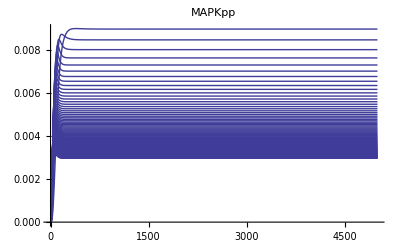

```mathematica
Plot[MAPKpp[0][t]/.dat,{t,0,tend},PlotLabel->"MAPKpp",PlotRange->All]
```

```mathematica
iftend=InterpolatingFunction[x__]:>InterpolatingFunction[x][tend];
GraphicsGrid[
Function[dat,
{{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]}/.dat/.iftend,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All],
ListLinePlot[{p1[0],Smem[0]}/.dat/.iftend,PlotLabel->"Smem"]
},{
ListLinePlot[{p1[0],(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat/.iftend,PlotLabel->"Sves"],
ListLinePlot[{p1[0],MAPKpp[0]}/.dat/.iftend,PlotLabel->"MAPKpp"]
}}]/@{dat,datSS}//Flatten[#,1]&,
ImageSize->Full]
```

ReplaceAll::reps: {dat} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListLinePlot::lpn: {C1[0] + C2[0] + C3[0] + C4[0] + C5[0] + C6[0] + C7[0] + C8[0] + C9[0], MAPKpp[0]}/. dat
 is not a list of numbers or pairs of numbers.

ReplaceAll::reps: {dat} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListLinePlot::lpn: {p1[0], Smem[0]}/. dat
 is not a list of numbers or pairs of numbers.

ReplaceAll::reps: {dat} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ListLinePlot::lpn: {p1[0], C1[0] + C2[0] + C3[0] + C4[0] + C5[0] + C6[0] + C7[0] + C8[0] + C9[0]}/. dat
 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

### runsim

```mathematica
eq={RAF'[t]==k2 RAFpRAFPh[t]-a1 RAF[t] (RAFKtot-RAFRAFKi[t])+d1 RAFRAFKi[t],RAFRAFKi'[t]==a1 RAF[t] (RAFKtot-RAFRAFKi[t])-(d1+k1) RAFRAFKi[t],RAFp'[t]==(d5+k5) MEKpRAFp[t]+(d3+k3) MEKRAFp[t]-a3 MEK[t] RAFp[t]-a5 MEKp[t] RAFp[t]-a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])+d2 RAFpRAFPh[t]+k1 RAFRAFKi[t],RAFpRAFPh'[t]==a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])-(d2+k2) RAFpRAFPh[t],MEK'[t]==of1 (C2[t]+C6[t]+C9[t])-on1 (C1[t]+C4[t]+C5[t]) MEK[t]+k4 MEKpMEKPh[t]+d3 MEKRAFp[t]-a3 MEK[t] RAFp[t],MEKRAFp'[t]==-(d3+k3) MEKRAFp[t]+a3 MEK[t] RAFp[t],MEKp'[t]==d4 MEKpMEKPh[t]-a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+k6 MEKppMEKPh[t]+d5 MEKpRAFp[t]+k3 MEKRAFp[t]-a5 MEKp[t] RAFp[t],MEKpMEKPh'[t]==-(d4+k4) MEKpMEKPh[t]+a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t]),MEKpRAFp'[t]==-(d5+k5) MEKpRAFp[t]+a5 MEKp[t] RAFp[t],MEKpp'[t]==of3 (C3[t]+C7[t]+C8[t])+(d7+k7) MAPKMEKpp[t]+(d9+k9) MAPKpMEKpp[t]-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+d6 MEKppMEKPh[t]+k5 MEKpRAFp[t],MEKppMEKPh'[t]==a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])-(d6+k6) MEKppMEKPh[t],MAPK'[t]==of2 (C4[t]+C6[t]+C7[t])-on2 (C1[t]+C2[t]+C3[t]) MAPK[t]+d7 MAPKMEKpp[t]+k8 MAPKpMAPKPh[t]-a7 MAPK[t] MEKpp[t],MAPKMEKpp'[t]==-(d7+k7) MAPKMEKpp[t]+a7 MAPK[t] MEKpp[t],MAPKp'[t]==k7 MAPKMEKpp[t]+d8 MAPKpMAPKPh[t]+d9 MAPKpMEKpp[t]-a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+k10 MAPKppMAPKPh[t]-a9 MAPKp[t] MEKpp[t],MAPKpMEKpp'[t]==-(d9+k9) MAPKpMEKpp[t]+a9 MAPKp[t] MEKpp[t],MAPKpp'[t]==of4 (C5[t]+C8[t]+C9[t])+k9 MAPKpMEKpp[t]-a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+d10 MAPKppMAPKPh[t],MAPKpMAPKPh'[t]==-(d8+k8) MAPKpMAPKPh[t]+a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t]),MAPKppMAPKPh'[t]==a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])-(d10+k10) MAPKppMAPKPh[t],C1'[t]==of1 C2[t]+of3 C3[t]+of2 C4[t]+of4 C5[t]-C1[t] (on2 MAPK[t]+on1 MEK[t]),C2'[t]==of2 C6[t]+of4 C9[t]-C2[t] (of1+on2 MAPK[t])+on1 C1[t] MEK[t]-k5 C2[t] RAFp[t],C3'[t]==-of3 C3[t]+of2 C7[t]+of4 C8[t]-on2 C3[t] MAPK[t]+k5 C2[t] RAFp[t],C4'[t]==of1 C6[t]+of3 C7[t]+on2 C1[t] MAPK[t]-C4[t] (of2+on1 MEK[t]),C5'[t]==of3 C8[t]+of1 C9[t]-C5[t] (of4+on1 MEK[t]),C6'[t]==-(of1+of2) C6[t]+on2 C2[t] MAPK[t]+on1 C4[t] MEK[t]-k5 C6[t] RAFp[t],C7'[t]==-k9 C7[t]-of2 C7[t]-of3 C7[t]+on2 C3[t] MAPK[t]+k5 C6[t] RAFp[t],C8'[t]==k9 C7[t]-(of3+of4) C8[t]+k5 C9[t] RAFp[t],C9'[t]==-(of1+of4) C9[t]+on1 C5[t] MEK[t]-k5 C9[t] RAFp[t]};
params={a1->1,a10->5,a2->0.5,a3->3.3,a4->10,a5->3.3,a6->10,a7->20,a8->5,a9->20,C1tot->0,d1->0.4,d10->0.4,d2->0.5,d3->0.42,d4->0.8,d5->0.4,d6->0.8,d7->0.6,d8->0.4,d9->0.6,k1->0.1,k10->0.1,k2->0.1,k3->0.1,k4->0.1,k5->0.1,k6->0.1,k7->0.1,k8->0.1,k9->0.1,MAPKPhtot->0.3,MAPKtot->0.4,MEKPhtot->0.2,MEKtot->0.2,of1->0.05,of2->0.05,of3->0.05,of4->0.5,on1->10,on2->10,RAFKtot->0.2 UnitStep[t],RAFPhtot->0.3,RAFtot->0.3};
tstart=-1000;
ic={RAF[-1000]==RAFtot,RAFRAFKi[-1000]==0,RAFp[-1000]==0,RAFpRAFPh[-1000]==0,MEK[-1000]==MEKtot,MEKRAFp[-1000]==0,MEKp[-1000]==0,MEKpMEKPh[-1000]==0,MEKpRAFp[-1000]==0,MEKpp[-1000]==0,MEKppMEKPh[-1000]==0,MAPK[-1000]==MAPKtot,MAPKMEKpp[-1000]==0,MAPKp[-1000]==0,MAPKpMEKpp[-1000]==0,MAPKpp[-1000]==0,MAPKpMAPKPh[-1000]==0,MAPKppMAPKPh[-1000]==0,C1[-1000]==C1tot,C2[-1000]==0,C3[-1000]==0,C4[-1000]==0,C5[-1000]==0,C6[-1000]==0,C7[-1000]==0,C8[-1000]==0,C9[-1000]==0};
len=2;
params=params/.Rule[RAFKtot,_]->Rule[RAFp,0.14]/.C1tot->Stot;
params=Join[params,{p2->0.1,p4->0.1,Di->0.001}];
params=Flatten[{params,Array[{p1[#]->0.1,p3[#]->0.1}&,len,0]}];
equ=Drop[eq,4];
equ=equ/.RAFp[t]->RAFp;
FluxCM=p1[s]*Scyto[t]-p2*Smem[t];
FluxMV=p3[s]*Smem[t];
FluxVC=p4*C1[t];
equ=equ/.C1'[t]==q_:>C1'[t]==q+(FluxMV-FluxVC);
equ=Join[
{Scyto'[t]==FluxVC-FluxCM},
equ,
{Smem'[t]==FluxCM-FluxMV}];
vars=equ[[All,1]];
vars=vars/.x_'[t]->x;
equ=equ/.Thread[vars->(#[s]&/@vars)];
equ=equ/.v_[s]'[t]==lhs_/;FreeQ[v,C1|C2|C3|C4|C5|C6|C7|C8|C9|Smem]->v[s]'[t]==lhs+Di(v[s-1][t]-2v[s][t]+v[s+1][t]);

equ=Flatten@Table[equ,{s,0,len-1}];
equ=equ/.{x_[-1][t]->x[0][t],x_[len][t]->x[len-1][t]};
vars=equ/.v_'[t]==_->v;
icODE=vars/.{MEK[s_]->MEK[s][0]==MEKtot,MAPK[s_]->MAPK[s][0]==MAPKtot,Scyto[s_]->Scyto[s][0]==Stot,v_[s_]->v[s][0]==0};
equODE=equ;
varODE=vars;

MEKtotequ=StringCases[ToString/@vars,___~~"MEK"~~___]//ToExpression//Flatten//Total;
MEKtotequ+=Sum[C2[s]+C3[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
MAPKtotequ=StringCases[ToString/@vars,___~~"MAPK"~~___]//ToExpression//Flatten//Total;
MAPKtotequ+=Sum[C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
Stotequ=Sum[C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}];

equ=equODE;
equ=DeleteCases[equ,MEK[0]'[t]==_];
equ=Append[equ,len*MEKtot==MEKtotequ];
equ=DeleteCases[equ,MAPK[0]'[t]==_];
equ=Append[equ,len*MAPKtot==MAPKtotequ];
equ=DeleteCases[equ,C1[0]'[t]==_];
equ=Append[equ,len*Stot==Sum[
C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}]];
equ=equ/.{x_'[t]->0,x_[t]->x};

tend=5000;
runsimODE[pp___]:=Block[{sol,p=Flatten[{pp}],ic=icODE,dtzero,tol=10^-8,maxiter=30,iter},
iter=Catch[
Do[
sol=NDSolve[Join[equODE,ic]//.p/.params,varODE,{t,0,tend}][[1]];
dtzero=Max@Abs[equODE[[All,2]]//.p/.t->tend/.sol/.params];
If[dtzero<tol,Throw[i]];
ic=vars/.x_[s_]:>x[s][0]==(x[s][tend]/.sol);
,{i,maxiter}]];
Join[{dd->dtzero,runsim$maxiter->(iter/.Null->maxiter)},p,sol]
];
runsim[pp___]:=Block[{sol},
sol=runsimODE[pp];
sol/.f_InterpolatingFunction->f[tend]
]
(*
runsimReinit[p___,s___]:=Module[{},
runsim$init=Thread[{
vars,
vars/.Flatten[{s}]/._->0,
Max[{MEKtot,MAPKtot,Stot}]/.Flatten[{p}]/.params}];
runsim$init=runsim$init[[All,{1,2}]];
]
runsimReinit[];
runsim[p___]:=Module[{sol},
sol=FindRoot[equ/.Flatten[{p}]/.params,runsim$init,MaxIterations->∞,DampingFactor->0.1];
If[
MatchQ[sol,{Rule[_,_?NumberQ]..}],
If[MatchQ[sol,{Rule[_,_?NonNegative]..}],
runsimReinit[p,sol]
],
runsimReinit[p];
];
Join[p,sol]
]
*)
dat=Table[
{s,MAPKpp[0]}/.runsim[p4->0,p2->0,Stot->s,p1[_]->100],
{s,0.192,0.202,0.0001}];
MAXMAPKPP=Max[dat[[All,2]]];
```

```mathematica
savefile="/data/mapk/mapk01.mx";
DeleteFile[savefile];
Save[savefile,{MAXMAPKPP,params,equ,vars,runsim,runsimODE,tend,equODE,icODE,varODE}];
```

```mathematica
Exit[]
```

```mathematica
dat=Table[
{s,MAPKpp[0]}/.runsim[p4->0,p2->0,Stot->s,p1[_]->100],
{s,0.0,2.0,0.01}];
```

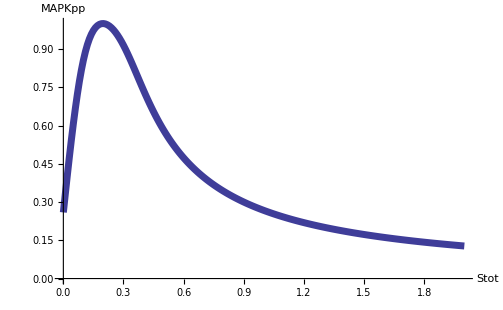

```mathematica
Block[{$TextStyle={"FontSize"->22}},
ListLinePlot[dat/.{s_,m_}->{s,m/MAXMAPKPP},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}]
]
```

### runsim-p4

```mathematica
eq={RAF'[t]==k2 RAFpRAFPh[t]-a1 RAF[t] (RAFKtot-RAFRAFKi[t])+d1 RAFRAFKi[t],RAFRAFKi'[t]==a1 RAF[t] (RAFKtot-RAFRAFKi[t])-(d1+k1) RAFRAFKi[t],RAFp'[t]==(d5+k5) MEKpRAFp[t]+(d3+k3) MEKRAFp[t]-a3 MEK[t] RAFp[t]-a5 MEKp[t] RAFp[t]-a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])+d2 RAFpRAFPh[t]+k1 RAFRAFKi[t],RAFpRAFPh'[t]==a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])-(d2+k2) RAFpRAFPh[t],MEK'[t]==of1 (C2[t]+C6[t]+C9[t])-on1 (C1[t]+C4[t]+C5[t]) MEK[t]+k4 MEKpMEKPh[t]+d3 MEKRAFp[t]-a3 MEK[t] RAFp[t],MEKRAFp'[t]==-(d3+k3) MEKRAFp[t]+a3 MEK[t] RAFp[t],MEKp'[t]==d4 MEKpMEKPh[t]-a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+k6 MEKppMEKPh[t]+d5 MEKpRAFp[t]+k3 MEKRAFp[t]-a5 MEKp[t] RAFp[t],MEKpMEKPh'[t]==-(d4+k4) MEKpMEKPh[t]+a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t]),MEKpRAFp'[t]==-(d5+k5) MEKpRAFp[t]+a5 MEKp[t] RAFp[t],MEKpp'[t]==of3 (C3[t]+C7[t]+C8[t])+(d7+k7) MAPKMEKpp[t]+(d9+k9) MAPKpMEKpp[t]-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+d6 MEKppMEKPh[t]+k5 MEKpRAFp[t],MEKppMEKPh'[t]==a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])-(d6+k6) MEKppMEKPh[t],MAPK'[t]==of2 (C4[t]+C6[t]+C7[t])-on2 (C1[t]+C2[t]+C3[t]) MAPK[t]+d7 MAPKMEKpp[t]+k8 MAPKpMAPKPh[t]-a7 MAPK[t] MEKpp[t],MAPKMEKpp'[t]==-(d7+k7) MAPKMEKpp[t]+a7 MAPK[t] MEKpp[t],MAPKp'[t]==k7 MAPKMEKpp[t]+d8 MAPKpMAPKPh[t]+d9 MAPKpMEKpp[t]-a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+k10 MAPKppMAPKPh[t]-a9 MAPKp[t] MEKpp[t],MAPKpMEKpp'[t]==-(d9+k9) MAPKpMEKpp[t]+a9 MAPKp[t] MEKpp[t],MAPKpp'[t]==of4 (C5[t]+C8[t]+C9[t])+k9 MAPKpMEKpp[t]-a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+d10 MAPKppMAPKPh[t],MAPKpMAPKPh'[t]==-(d8+k8) MAPKpMAPKPh[t]+a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t]),MAPKppMAPKPh'[t]==a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])-(d10+k10) MAPKppMAPKPh[t],C1'[t]==of1 C2[t]+of3 C3[t]+of2 C4[t]+of4 C5[t]-C1[t] (on2 MAPK[t]+on1 MEK[t]),C2'[t]==of2 C6[t]+of4 C9[t]-C2[t] (of1+on2 MAPK[t])+on1 C1[t] MEK[t]-k5 C2[t] RAFp[t],C3'[t]==-of3 C3[t]+of2 C7[t]+of4 C8[t]-on2 C3[t] MAPK[t]+k5 C2[t] RAFp[t],C4'[t]==of1 C6[t]+of3 C7[t]+on2 C1[t] MAPK[t]-C4[t] (of2+on1 MEK[t]),C5'[t]==of3 C8[t]+of1 C9[t]-C5[t] (of4+on1 MEK[t]),C6'[t]==-(of1+of2) C6[t]+on2 C2[t] MAPK[t]+on1 C4[t] MEK[t]-k5 C6[t] RAFp[t],C7'[t]==-k9 C7[t]-of2 C7[t]-of3 C7[t]+on2 C3[t] MAPK[t]+k5 C6[t] RAFp[t],C8'[t]==k9 C7[t]-(of3+of4) C8[t]+k5 C9[t] RAFp[t],C9'[t]==-(of1+of4) C9[t]+on1 C5[t] MEK[t]-k5 C9[t] RAFp[t]};
params={a1->1,a10->5,a2->0.5,a3->3.3,a4->10,a5->3.3,a6->10,a7->20,a8->5,a9->20,C1tot->0,d1->0.4,d10->0.4,d2->0.5,d3->0.42,d4->0.8,d5->0.4,d6->0.8,d7->0.6,d8->0.4,d9->0.6,k1->0.1,k10->0.1,k2->0.1,k3->0.1,k4->0.1,k5->0.1,k6->0.1,k7->0.1,k8->0.1,k9->0.1,MAPKPhtot->0.3,MAPKtot->0.4,MEKPhtot->0.2,MEKtot->0.2,of1->0.05,of2->0.05,of3->0.05,of4->0.5,on1->10,on2->10,RAFKtot->0.2 UnitStep[t],RAFPhtot->0.3,RAFtot->0.3};
tstart=-1000;
ic={RAF[-1000]==RAFtot,RAFRAFKi[-1000]==0,RAFp[-1000]==0,RAFpRAFPh[-1000]==0,MEK[-1000]==MEKtot,MEKRAFp[-1000]==0,MEKp[-1000]==0,MEKpMEKPh[-1000]==0,MEKpRAFp[-1000]==0,MEKpp[-1000]==0,MEKppMEKPh[-1000]==0,MAPK[-1000]==MAPKtot,MAPKMEKpp[-1000]==0,MAPKp[-1000]==0,MAPKpMEKpp[-1000]==0,MAPKpp[-1000]==0,MAPKpMAPKPh[-1000]==0,MAPKppMAPKPh[-1000]==0,C1[-1000]==C1tot,C2[-1000]==0,C3[-1000]==0,C4[-1000]==0,C5[-1000]==0,C6[-1000]==0,C7[-1000]==0,C8[-1000]==0,C9[-1000]==0};
len=2;
params=params/.Rule[RAFKtot,_]->Rule[RAFp,0.14]/.C1tot->Stot;
params=Join[params,{p2->0.1,Di->0.0001}];
params=Flatten[{params,Array[{p1[#]->0.1,p3[#]->0.1,p4[#]->0.1}&,len,0]}];
equ=Drop[eq,4];
equ=equ/.RAFp[t]->RAFp;
FluxCM=p1[s]*Scyto[t]-p2*Smem[t];
FluxMV=p3[s]*Smem[t];
FluxVC=p4[s]*C1[t];
equ=equ/.C1'[t]==q_:>C1'[t]==q+(FluxMV-FluxVC);
equ=Join[
{Scyto'[t]==FluxVC-FluxCM},
equ,
{Smem'[t]==FluxCM-FluxMV}];
vars=equ[[All,1]];
vars=vars/.x_'[t]->x;
equ=equ/.Thread[vars->(#[s]&/@vars)];
equ=equ/.v_[s]'[t]==lhs_/;FreeQ[v,C1|C2|C3|C4|C5|C6|C7|C8|C9|Smem]->v[s]'[t]==lhs+Di(v[s-1][t]-2v[s][t]+v[s+1][t]);

equ=Flatten@Table[equ,{s,0,len-1}];
equ=equ/.{x_[-1][t]->x[0][t],x_[len][t]->x[len-1][t]};
vars=equ/.v_'[t]==_->v;
icODE=vars/.{MEK[s_]->MEK[s][0]==MEKtot,MAPK[s_]->MAPK[s][0]==MAPKtot,Scyto[s_]->Scyto[s][0]==Stot,v_[s_]->v[s][0]==0};
equODE=equ;
varODE=vars;

MEKtotequ=StringCases[ToString/@vars,___~~"MEK"~~___]//ToExpression//Flatten//Total;
MEKtotequ+=Sum[C2[s]+C3[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
MAPKtotequ=StringCases[ToString/@vars,___~~"MAPK"~~___]//ToExpression//Flatten//Total;
MAPKtotequ+=Sum[C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
Stotequ=Sum[C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}];

equ=equODE;
equ=DeleteCases[equ,MEK[0]'[t]==_];
equ=Append[equ,len*MEKtot==MEKtotequ];
equ=DeleteCases[equ,MAPK[0]'[t]==_];
equ=Append[equ,len*MAPKtot==MAPKtotequ];
equ=DeleteCases[equ,C1[0]'[t]==_];
equ=Append[equ,len*Stot==Sum[
C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}]];
equ=equ/.{x_'[t]->0,x_[t]->x};

tend=5000;
runsimODE[pp___]:=Block[{sol,p=Flatten[{pp}],ic=icODE,dtzero,tol=10^-8,maxiter=30,iter},
iter=Catch[
Do[
sol=NDSolve[Join[equODE,ic]//.p/.params,varODE,{t,0,tend}][[1]];
dtzero=Max@Abs[equODE[[All,2]]//.p/.t->tend/.sol/.params];
If[dtzero<tol,Throw[i]];
ic=vars/.x_[s_]:>x[s][0]==(x[s][tend]/.sol);
,{i,maxiter}]];
Join[{dd->dtzero,runsim$maxiter->(iter/.Null->maxiter)},p,sol]
];
runsim[pp___]:=Block[{sol},
sol=runsimODE[pp];
sol/.f_InterpolatingFunction->f[tend]
]
(*
runsimReinit[p___,s___]:=Module[{},
runsim$init=Thread[{
vars,
vars/.Flatten[{s}]/._->0,
Max[{MEKtot,MAPKtot,Stot}]/.Flatten[{p}]/.params}];
runsim$init=runsim$init[[All,{1,2}]];
]
runsimReinit[];
runsim[p___]:=Module[{sol},
sol=FindRoot[equ/.Flatten[{p}]/.params,runsim$init,MaxIterations->∞,DampingFactor->0.1];
If[
MatchQ[sol,{Rule[_,_?NumberQ]..}],
If[MatchQ[sol,{Rule[_,_?NonNegative]..}],
runsimReinit[p,sol]
],
runsimReinit[p];
];
Join[p,sol]
]
*)
dat=Table[
{s,MAPKpp[0]}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],
{s,0.192,0.202,0.0001}];
MAXMAPKPP=Max[dat[[All,2]]];
```

```mathematica
savefile="/data/mapk/mapkp4.mx";
DeleteFile[savefile];
Save[savefile,{MAXMAPKPP,params,equ,vars,runsim,runsimODE,tend,equODE,icODE,varODE}];
```

```mathematica
Exit[]
```

```mathematica
dat=Table[
{s,MAPKpp[0]}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],
{s,0.0,2.0,0.01}];
```

```mathematica
Block[{$TextStyle={"FontSize"->22}},
ListLinePlot[dat/.{s_,m_}->{s,m/MAXMAPKPP},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}]
]
```

-Graphics-

### MI vs dose

```mathematica
Get["/data/mapk/mapk01.mx"];
ParallelEvaluate[$KernelID]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
params=Join[{p3a->0.3346907375872372,p3b->0.021907428393711043,p3c->10.009922451106727,p3d->0.,p2->0.11608892872854891,p4->0.26341348521212116,p5->0.9818805143581429},params];
```

```mathematica
StotNative=0.1;
StotOE=2.0;
dose=Range[0.01,1.0,0.01];
Length[dose]
```

100

```mathematica
v={p1[0],p2,p3[0],p3[1],p4,p5};
TableForm[{v,v/.params}]
```

p1[0] | p2 | p3[0] | p3[1] | p4 | p5
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | p5

```mathematica
dat=Transpose@ParallelTable[
plist={Stot->s,p1[0]->p5*d,p1[1]->p5*d,p2->0.1,p3[_]->0.1,p4->0.1}/.{p5->0.01};
runsim[plist]
,{d,dose},{s,{StotNative,StotOE}},Method->"FinestGrained"];
Dimensions[dat]
```

{2,100,58}

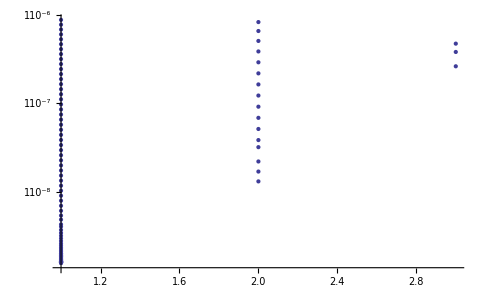

```mathematica
{runsim$maxiter,dd}/.dat//ListLogPlot
```

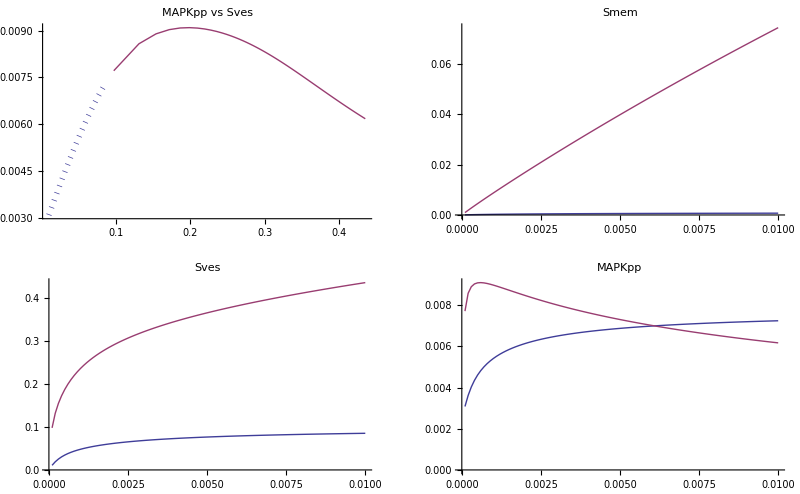

```mathematica
GraphicsGrid[{
{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All],
ListLinePlot[{p1[0],Smem[0]}/.dat,PlotLabel->"Smem"]
},{
ListLinePlot[{p1[0],(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{p1[0],MAPKpp[0]}/.dat,PlotLabel->"MAPKpp"]
}},ImageSize->Full]
```

Unset::norep: Assignment on Smem for Smem[0] not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

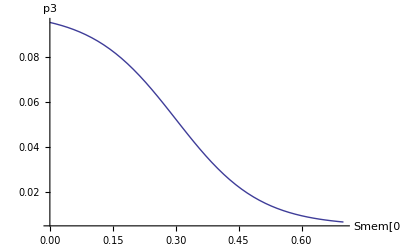

```mathematica
p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[p3c(Smem[s][t]-p3a)])+p3d]/@{0,1};
p3list={p3a->0.3,p3b->0.1,p3c->10,p3d->0.005};
Plot[p3[0]/.p3sigmoid/.p3list//Evaluate,{Smem[0][t],0,0.7},PlotRange->All,AxesLabel->{"Smem[0]","p3"}]
```

```mathematica
plist={}
DoseResponse[stot_]:=Module[{},
Function[m,
plist=Join[
p3sigmoid/.p3list,
{p1[0]->m,p1[1]->m,p1->m,Stot->stot}
];
runsim[plist]
]~ParallelMap~dose
];
dat=Map[DoseResponse,{StotNative,StotOE}];
Dimensions[dat]
```

{}

{2,100,58}

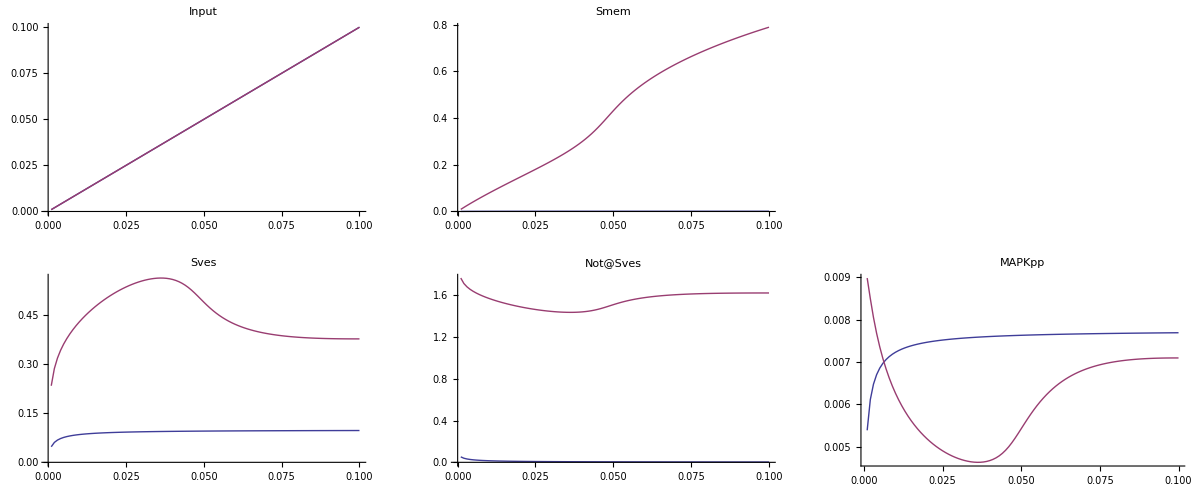

```mathematica
GraphicsGrid[{
{ListLinePlot[{p1,p1}/.dat,PlotLabel->"Input"],
ListLinePlot[{p1,Smem[0]}/.plist/.dat,PlotLabel->"Smem"],
ListLinePlot[{p1,p3[0]}/.plist/.x_[t]->x/.dat,PlotLabel->"p3[Smem[i]]"]},
{ListLinePlot[{p1,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{p1,Stot-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Not@Sves"],
ListLinePlot[{p1,MAPKpp[0]}/.dat,PlotRange->All,PlotLabel->"MAPKpp"]}
},ImageSize->Full]
```

```mathematica
DoseResponse[stot_]:=Module[{dat},
dat=Function[d,
plist=Join[
p3sigmoid/.p3list,
{p1[0]->d,p1[1]->d+0.005,Stot->stot,Di->0.000001}
];
runsim[plist]
]~ParallelMap~dose;
dat
];
dat=DoseResponse[StotNative];
Dimensions[dat]
```

{100,58}

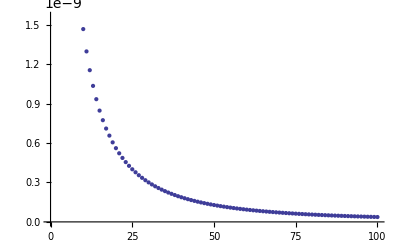

```mathematica
dd/.dat//ListPlot
```

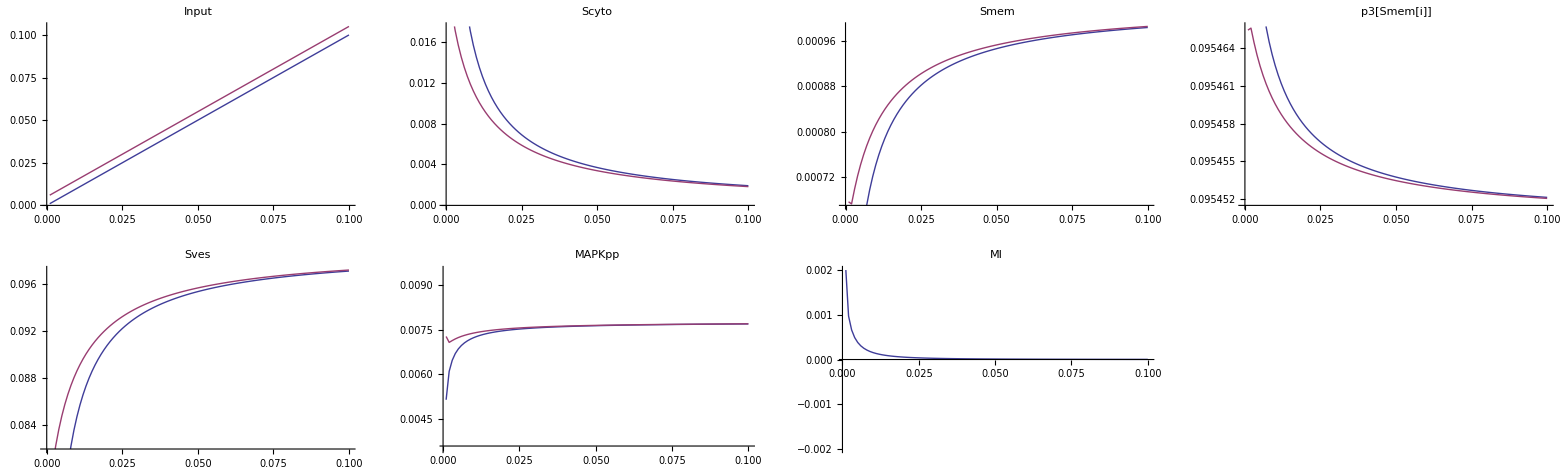

```mathematica
GraphicsGrid[{{
ListLinePlot[{{p1[0],p1[0]},{p1[0],p1[1]}}/.dat//Transpose,PlotLabel->"Input"],
ListLinePlot[{{p1[0],Scyto[0]},{p1[0],Scyto[1]}}/.dat//Transpose,PlotLabel->"Scyto"],
ListLinePlot[{{p1[0],Smem[0]},{p1[0],Smem[1]}}/.dat//Transpose,PlotLabel->"Smem"],
ListLinePlot[{{p1[0],p3[0]},{p1[0],p3[1]}}//.dat/.x_[t]->x//Transpose,PlotLabel->"p3[Smem[i]]"]
},{
ListLinePlot[{
{p1[0],(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])},
{p1[0],(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])}
}/.dat//Transpose,PlotLabel->"Sves"],
ListLinePlot[{{p1[0],MAPKpp[0]},{p1[0],MAPKpp[1]}}/.dat//Transpose,PlotRange->3 10^-3{-1,1}+0.0065,PlotLabel->"MAPKpp"],
ListLinePlot[{p1[0],MAPKpp[1]-MAPKpp[0]}/.dat,PlotRange->2 10^-3{-1,1},PlotLabel->"MI"]
}},ImageSize->Full]
```

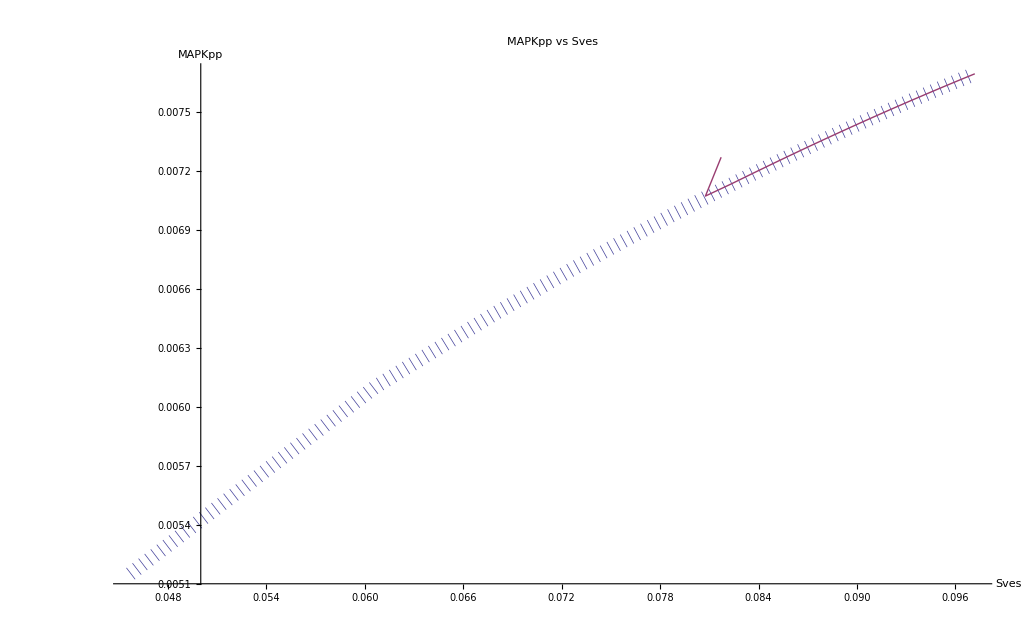

```mathematica
ListLinePlot[{
{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]},
{(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1]),MAPKpp[1]}}/.dat//Transpose,
PlotRange->All,PlotLabel->"MAPKpp vs Sves",AxesLabel->{"Sves","MAPKpp"},PlotStyle->{{Dotted,Thickness[0.01]},Thick}]
```

### Optimization

```mathematica
Exit[]
```

```mathematica
Get["/data/mapk/mapk01.mx"];
Get["/home/abergman/dicty/SPSA.m"]
ParallelEvaluate[$KernelID]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
StotNative=0.1;
StotOE=2.0;
dose=Range[0.01,1.0,0.01];
p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[p3c(Smem[s][t]-p3a)])+p3d]/@{0,1};
p3list={p3a->0.3,p3b->0.1,p3c->10,p3d->0.005};
Plot[p3[0]/.p3sigmoid/.p3list//Evaluate,{Smem[0][t],0,0.7},PlotRange->All,AxesLabel->{"Smem[0]","p3"}]
```

Unset::norep: Assignment on Smem for Smem[0] not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

-Graphics-

```mathematica
θ0={0.5,0.1,0.2,0.1};
v={p2,p3b,p4,p5};
Loss[θ_?(VectorQ[#,NumericQ]&)]:=Module[{pθ=Thread[v->θ]},
dat=Transpose@ParallelTable[
plist=Join[
{Stot->stot,p1[0]->p5*d,p1[1]->p5*(d+0.005),p3[_]->p3b}/.pθ,
pθ
];
runsim[plist]
,{d,dose},{stot,{StotNative}},Method->"FinestGrained"];

{MIsimNative}=MAPKpp[1]-MAPKpp[0]/.dat;

MIerror=Function[{xrng,MIsim,MIuser},
d=Thread[xrng[[1]]<dose<xrng[[2]]];
Mean@Abs[(MIuser/@Pick[dose,d])-Pick[MIsim,d]]
]~MapThread~{Partition[ptsuser[[All,1]],2],{MIsimNative},{MIuserNative}};

Total[MIerror]
]
Loss[θ0]
```

2.57788×10^-6

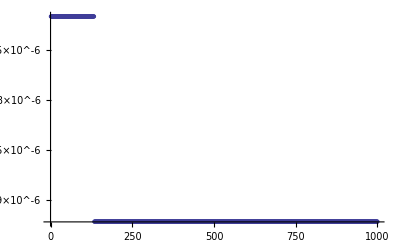

```mathematica
MyConstraints=Clip[#1,{0.0,50}]&;
SPSAConstraints[MyConstraints];
SPSAMaxEvals[10^3]
sol=RandomSearch[Loss,θ0,10^-4];
θ0=sol[[-1,2]];
Loss[θ0]
ListLogPlot[sol[[All,1]]]
```

```mathematica
xrng=dose[[{1,-1}]];
ptsuser=Thread[{xrng,0}];
Off[InterpolatingFunction::dmval]
```

```mathematica
LocatorPane[Dynamic[ptsuser],
Dynamic[
MIuserNative=Interpolation[ptsuser,InterpolationOrder->1];
ListLinePlot[{{#,MIuserNative[#]}&/@dose,{dose,MIsimNative}ᵀ},PlotRange->10^-4{-1,1},ImageSize->Full,PlotMarkers->Automatic]
]]
```

```mathematica
Dynamic@GraphicsGrid[{
{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All],
ListLinePlot[{p1[0],Smem[0]}/.dat,PlotLabel->"Smem"]
},{
ListLinePlot[{p1[0],(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves",PlotRange->All],
ListLinePlot[{p1[0],MAPKpp[0]}/.dat,PlotLabel->"MAPKpp",PlotRange->All]
}},ImageSize->Full]
```

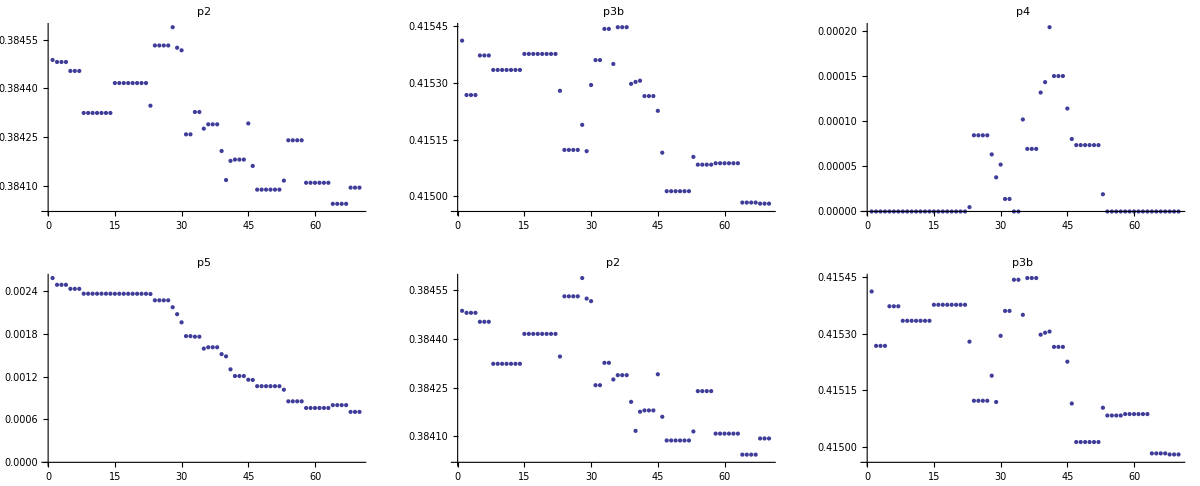

```mathematica
GraphicsGrid[MapThread[Function[{v,p},ListPlot[p,PlotLabel->ToString[v]]],{v,sol[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
```

### Opt

```mathematica
Thread[Rule[v,θ0]]
```

{p3a→0.334691,p3b→0.0219074,p3c→10.0099,p3d→0.,p2→0.116089,p4→0.263413,p5→0.981881}

```mathematica
θ0={0.3346907375872372,0.021907428393711043,10.009922451106727,0.,0.11608892872854891,0.26341348521212116,0.9818805143581429}
```

{0.334691,0.0219074,10.0099,0.,0.116089,0.263413,0.981881}

```mathematica
TableForm[{v,θ0}]
```

p3a | p3b | p3c | p3d | p2 | p4 | p5
0.334691 | 0.0219074 | 10.0099 | 0. | 0.116089 | 0.263413 | 0.981881

```mathematica
θ0={0.3,0.1,10,0.005,0.1,0.2,1};
v={p3a,p3b,p3c,p3d,p2,p4,p5};
```

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=Module[{pθ=Thread[v->θ]},
dat=Transpose@ParallelTable[
plist=Join[
p3sigmoid/.pθ/.p3list,
{p1[0]->p5*d,p1[1]->p5*(d+0.005),Stot->stot,Di->0.000001}/.pθ,
pθ
];
runsim[plist]
,{d,dose},{stot,{StotNative,StotOE}},Method->"FinestGrained"];

{MIsimNative,MIsimOE}=MAPKpp[1]-MAPKpp[0]/.dat;

MIerror=Function[{xrng,MIsim,MIuser},
d=Thread[xrng[[1]]<dose<xrng[[2]]];
Mean@Abs[(MIuser/@Pick[dose,d])-Pick[MIsim,d]]
]~MapThread~{Partition[ptsuser[[All,1]],2],{MIsimNative,MIsimOE},{MIuserNative,MIuserOE}};

Total[MIerror]
]
Loss[θ0]
```

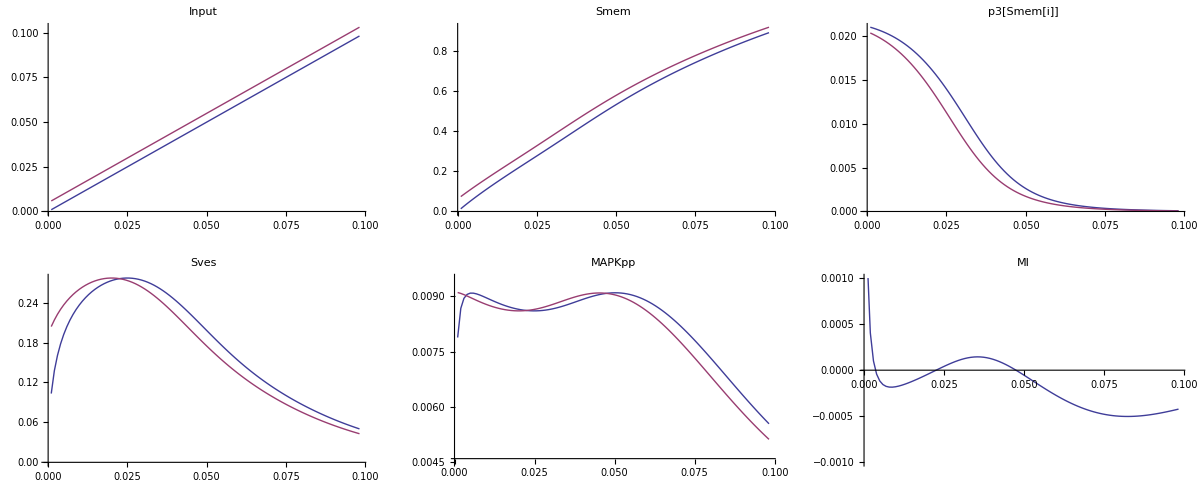

```mathematica
Function[dat,GraphicsGrid[{
{ListLinePlot[{{p1[0],p1[0]},{p1[0],p1[1]}}/.dat//Transpose,PlotLabel->"Input"],
ListLinePlot[{{p1[0],Smem[0]},{p1[0],Smem[1]}}/.dat//Transpose,PlotLabel->"Smem"],
ListLinePlot[{{p1[0],p3[0]},{p1[0],p3[1]}}//.(dat/.x_[t]->x)//Transpose,PlotLabel->"p3[Smem[i]]"]},
{ListLinePlot[{
{p1[0],(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])},
{p1[0],(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])}
}/.dat//Transpose,PlotLabel->"Sves"],
ListLinePlot[{{p1[0],MAPKpp[0]},{p1[0],MAPKpp[1]}}/.dat//Transpose,PlotRange->10^-3{-2,3}+0.0065,PlotLabel->"MAPKpp"],ListLinePlot[{p1[0],MAPKpp[1]-MAPKpp[0]}/.dat,PlotRange->10^-3{-1,1},PlotLabel->"MI"]}
},ImageSize->Full]][dat[[2]]]
```

0.0000903253

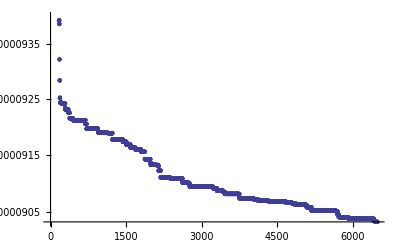

```mathematica
MyConstraints=Clip[#1,{0.0,50}]&;
SPSAConstraints[MyConstraints];
SPSAMaxEvals[10^5]
sol=RandomSearch[Loss,θ0,10^{-3,-3,-3,-3,-3,-3,-3}];
θ0=sol[[-1,2]];
Loss[θ0]
ListLogPlot[sol[[All,1]]]
```

```mathematica
xrng={0.01,0.05};
ptsuser=Thread[{xrng,0}];
ptsuser=Join[ptsuser,ptsuser]
Off[InterpolatingFunction::dmval]
```

{{0.01,0},{0.05,0},{0.01,0},{0.05,0}}

```mathematica
Off[InterpolatingFunction::dmval]
```

```mathematica
LocatorPane[Dynamic[ptsuser],
Dynamic[
{MIuserNative,MIuserOE}=Interpolation[#,InterpolationOrder->1]&/@Partition[ptsuser,2];
ListLinePlot[{
{#,MIuserNative[#]}&/@dose,{#,MIuserOE[#]}&/@dose,
{dose,MIsimNative}ᵀ,{dose,MIsimOE}ᵀ},PlotRange->10^-3{-1,1},ImageSize->Full,PlotMarkers->Automatic]
]]
```

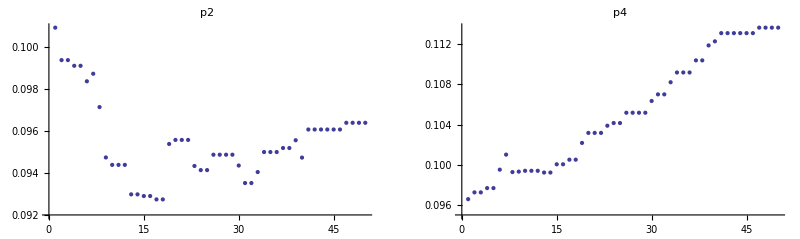

```mathematica
GraphicsGrid[List@MapThread[Function[{v,p},ListPlot[p,PlotLabel->ToString[v]]],{v,sol[[All,2]]ᵀ}],ImageSize->Full]
```

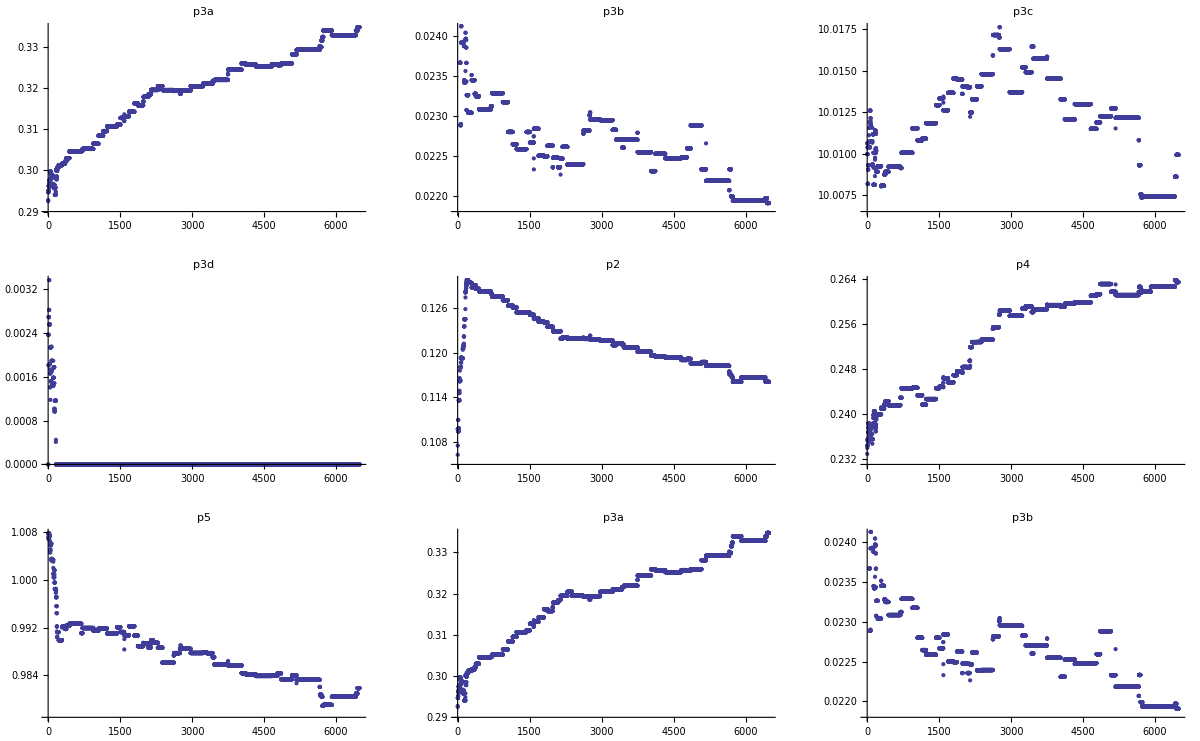

```mathematica
GraphicsGrid[MapThread[Function[{v,p},ListPlot[p,PlotLabel->ToString[v]]],{v,sol[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
```